# FCF Ideas

## Basic Math

We start with the basic Franck-Condon type electronic model, i.e. we have plots like

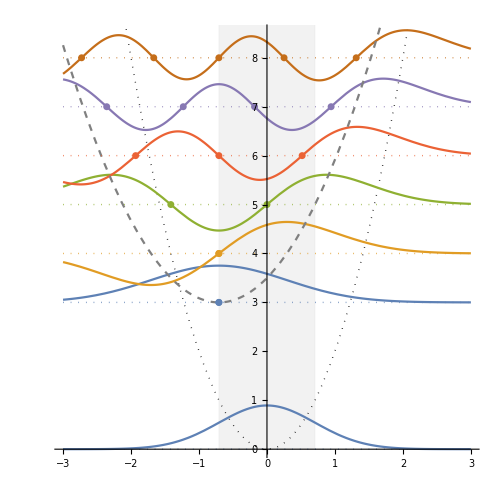

and then our idea will be to rotate the normal mode coordinates so that we have an effective normal mode that’s unitarily equivalent to the original normal modes that connects the two minima on the surface. It should be noted that in the case that there truly is one unique coordinate that connects the minima this rotation will do nothing

The rotation method is simple, we need only to compute Δξ, the vector connecting the two minima (in an Eckart frame), and then use least squares to find a transformation vector w that expresses Δξ in the basis of the normal modes of one of our structures

As w is normalized and we can imagine finding a basis of corresponding orthonormal vectors the G matrix remains the identity after applying this transformation, therefore the KE is not complicated by this transformation and we can define a local frequency with respect to these

### Franck-Condon Math

We start with two basis functions

ϕ^(g.s.)(r^(g.s.)) = ℋ_n(...)exp(-1/2(r^(g.s.) - c^(g.s.))^T Ω^(g.s.)(r^(g.s.) - c^(g.s.)))
ϕ^(e.s.)(r^(e.s.)) = ℋ_m(...)exp(-1/2(r^(e.s.) - c^(e.s.))^T Ω^(e.s.)(r^(e.s.) - c^(e.s.)))

where Ω^(...) is diagonal with the frequencies on the diagonals

The hard part here is computing the appropriate Gaussian integrals in the rotated frame. To do that, we’ll start with the transformations from coordinates to modes

L^(g.s.) = ∇_X R^(g.s.)
L^(e.s.)= ∇_X R^(e.s.)

this gives us an approximate transformation between modes

Q^(g,e) = L^((g.s.)-1)L^(e.s.) = ∇_(R^(g.s.)) R^(e.s.)

so assuming a linear relationship, we can reexpress the g.s. basis function in the e.s. coordinate frame by writing

(r^(e.s.))^T ≃ (r^(g.s.))^T Q^(g,e) + (c^(g.s.) - c^(e.s))Q^(g,e)

plugging that in, we get

((r^(g.s.))^T Q^(g,e) - c^(e.s.))^T Ω^(e.s.)=

(r^(e.s.))^T ≃ (r^(g.s.))^T Q^(g,e)

giving us

ϕ^(g.s.)(r^(g.s.)) = ℋ_n(...)exp(-1/2(r^(g.s.) - c^(g.s.))Ω^(g.s.)(r^(g.s.) - c^(g.s.)))
ϕ^(e.s.)(r^(e.s.)) = ℋ_m(...)exp(-1/2(r^(e.s.) - c^(g.s.))Ω^(g.s.)(r^(e.s.) - c^(g.s.)))

## HO Simple Ideas

##### Setup

```mathematica
ClearAll[hoParab, hoNorm,hoWfn, hoPolyIntegral,
hoOvIntegrate,prodNorm,prodPoly,prodGaussOv];
hoParab[a_, x0_][x_]:=
a(x-x0)^2;
hoNorm[n_, a_]:=
(a/π)^(1/4)/Sqrt[2^n * n!];
hoWfn[n_,a_,x0_][x_]:=
hoNorm[n, a]*Exp[-1/2 a(x-x0)^2]*HermiteH[n,Sqrt[a]*(x-x0)];
hoPolyIntegral[k_, a_]:=
2^(1/2 (-1+k)) (1+(-1)^k) a^(-1/2-k/2) Gamma[(1+k)/2];
hoOvIntegrate[
{n1_,a1_, x1_},
{n2_, a2_, x2_}
]:=
Block[{xc, ac, px,pref, pCoeffs},
ac=(a1+a2);
xc=(a1*x1+a2*x2)/ac;
pref=hoNorm[n1, a1]*hoNorm[n2,a2]*(
Exp[-a1 a2 /(2 (a1+a2))(x1-x2)^2]
);
px=HermiteH[n1, Sqrt[a1]*(x-x1)]*HermiteH[n2, Sqrt[a2]*(x-x2)];
px=px/.x->(x+xc);
pCoeffs=CoefficientList[px, x];
pref*(
pCoeffs.Table[hoPolyIntegral[k, ac], {k, 0,Length@pCoeffs-1}]
)
];
prodNorm[prod:{__List}]:=
Times@@((#2/π)^(1/4)&@@@prod);
prodPoly[prod:{__List}, baseVar_]:=
Times@@MapIndexed[
HermiteH[#[[1]], Sqrt[#[[2]]]*(baseVar[#2[[1]]]-#[[3]])]/Sqrt[2^#[[1]] * #[[1]]!]&,
prod
]/.baseVar[i_]:>baseVar[Floor[i]];
prodGaussian[prod_, baseVar_]:=
Times@@MapIndexed[
Exp[-1/2#[[2]](baseVar[#2[[1]]]-#[[3]])^2]&,
prod
]/.baseVar[i_]:>baseVar[Floor[i]];
prodWfn[prod:{__List}, baseVar_]:=
prodNorm[prod]*prodPoly[prod, baseVar]*prodGaussian[prod, baseVar];
prodGaussOv[
gsProd:{__List},
esProd:{__List},
tfMat_
]:=
Block[{Σg, Σe, L, cg, ce,center, alphas, poly,Sc, dx, prefactor,
X, Y},
Σg=tfMat.DiagonalMatrix[#[[2]]&/@gsProd].Transpose[tfMat];
Σe=DiagonalMatrix[#[[2]]&/@esProd];
{alphas, L}=Eigensystem[Σg+Σe];
cg=#[[3]]&/@gsProd;
ce=#[[3]]&/@esProd;
center=Inverse[Σg+Σe].(Σg.tfMat.cg+ Σe.ce);
Sc=Inverse[Inverse[Σg]+Inverse[Σe]];
dx=tfMat.cg-ce;
prefactor=prodNorm[gsProd]*prodNorm[esProd]*Exp[-1/2*(dx.Sc.dx)];
X=Array[x, Length@tfMat];
Y=Array[y, Length@tfMat];
poly=prodPoly[esProd, x]*
prodPoly[gsProd, y]/.Thread[
Y->tfMat.X
];
poly=poly/.Thread[X->X+center];
poly=poly/.Thread[X->Transpose[L].X];
{prefactor,alphas, poly}
];
hoOvNumIntegrate[
gsProd:{__List},
esProd:{__List},
tfMat_
]:=
Block[{xxx},
NIntegrate@@ReplaceAll[
Prepend[
prodWfn[esProd, x]*
prodWfn[gsProd, y]/.Thread[
Array[y, Length@tfMat]->Transpose[tfMat].Array[x, Length@tfMat]
]
]@Table[
{x[i],-∞, ∞},
{i, Length@tfMat}
],
x[i_]:>Symbol["xxx"<>ToString[i]]
]
];
hoOvIntegrate[
gsProd:{__List},
esProd:{__List},
tfMat_,
returnComps:True|False:False
]:=
Block[{pref, alphas, poly, coeffs},
{pref, alphas, poly}=prodGaussOv[gsProd, esProd, tfMat];
coeffs=CoefficientList[Expand@poly, Array[x, Length@tfMat]];
If[returnComps, Identity, 
#[[1]]*#[[2]].#[[3]]&
]@{
pref,
Flatten[coeffs],
Table[
If[coeffs[[Sequence@@idx]]!=0.,
Times@@MapIndexed[hoPolyIntegral[#-1, alphas[[#2[[1]]]]]&, idx],
0
],
{idx, Tuples[Map[Range, Dimensions@coeffs]]}
],
Dimensions@coeffs
}
];
hoOvIntegrateBreakdown[
gsProd:{__List},
esProd:{__List},
tfMat_
]:=
Block[{pref, coeff, ints, dims},
{pref, coeff, ints, dims}=hoOvIntegrate[
gsProd,
esProd,
tfMat,
True
];
{
pref,
Thread[
Tuples[Map[Range, dims]]->coeff*ints
]//GroupBy[Total@*First->Last],
Thread[
Tuples[Map[Range, dims]]->coeff
]//GroupBy[Total@*First->Last],
Thread[
Tuples[Map[Range, dims]]->ints
]//GroupBy[Total@*First->Last]
}
]
ClearAll[hoPlot];
Options[hoPlot]=DeleteDuplicatesBy[First]@Flatten@{
"PotentialScaling"->1,
"PotentialStyle"->{
PlotStyle->Directive[Dashed, Gray]
},
"ShowPotential"->True,
"ShowWavefunctions"->True,
"ShowZeros"->False,
"ZerosStyle"->{
PlotStyle->AbsolutePointSize[5]
},
"ShowBaselines"->True,
"EnergyShift"->0,
Options[Plot]
};
hoPlot[
nMax_, a_, x0_,
Optional[{xMin_, xMax_}, {-5, 5}],
ops:OptionsPattern[]
]:=
With[{
plops=FilterRules[{ops, PlotRange->All}, Options[Plot]],
potops=OptionValue["PotentialStyle"],
zerosops=OptionValue["ZerosStyle"]
},
Show@@{
If[TrueQ@OptionValue["ShowWavefunctions"],
Plot[
Table[
OptionValue["EnergyShift"]+n+hoWfn[n, a, x0][x],
{n, 0, nMax}
]//Evaluate,
{x, xMin, xMax},
plops
],
Nothing
],
If[TrueQ@OptionValue["ShowPotential"],
Plot[
OptionValue["EnergyShift"]+OptionValue["PotentialScaling"]*hoParab[a, x0][x]//Evaluate,
{x, xMin, xMax},
potops
],
Nothing
],
If[TrueQ@OptionValue["ShowZeros"],
ListPlot[
Table[
If[n==0,
{{x0,OptionValue["EnergyShift"]}},
Thread@{x0+1/a*hermiteRoots[n],OptionValue["EnergyShift"]+n}
],
{n, 0, 5}
],
zerosops
],
Nothing
],
If[TrueQ@OptionValue["ShowBaselines"],
ListLinePlot[
Table[{{xMin, OptionValue["EnergyShift"]+n}, {xMax, OptionValue["EnergyShift"]+n}}, {n, 0, nMax}],
PlotStyle->Directive[AbsoluteThickness[1], Dotted]
],
Nothing
]
}
];
hermiteRoots[n_]:=
Sort[
Eigenvalues[
N[SparseArray[{{j_,k_}/;Abs[j-k]==1:>Sqrt[Min[j,k]/2]},{n,n}]]
]
];
```

```mathematica
Clear[fcfList];
fcfList[{sg_, se_}, r_, nMax:Integer_:7]:=
Table[
hoOvIntegrate[
{0, sg, 0},
{n, se, r}
],
{n, 0, nMax}
];
fcfList[s_?NumericQ, r_, nMax:Integer_:7]:=
fcfList[{s, 1}, r, nMax]
```

##### Plots

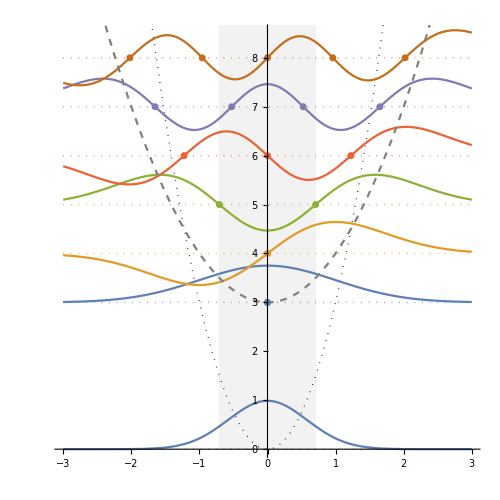

```mathematica
Show[
hoPlot[0, 3, 0,
{-3, 3},
"PotentialStyle"->{
PlotStyle->Directive[AbsoluteThickness[1], Black,Dotted]
}
],
hoPlot[5, 1, 0,
{-3, 3},
 "EnergyShift"->3,
"ShowZeros"->True
],
PlotRange->{0, 8.5},
Prolog->{
{
Dashed,
Gray,
Opacity[.1],
EdgeForm[Opacity[.05]],
Rectangle[{-r1, 0}, {r1, 15}]
}
},
ImageSize->{500, 500},
AspectRatio->Full
](*//imageify//Export[FileNameJoin@{NotebookDirectory[], "shift_gs.png"}, #]&*)
```

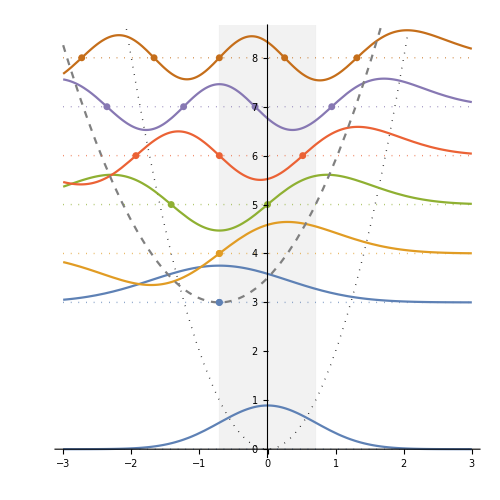

```mathematica
Show[
hoPlot[0, 2, 0,
{-3, 3},
"PotentialStyle"->{
PlotStyle->Directive[AbsoluteThickness[1], Black,Dotted]
}
],
hoPlot[5, 1, r1,
{-3, 3},
 "EnergyShift"->3,
"ShowZeros"->True
],
PlotRange->{0, 8.5},
Prolog->{
{
Dashed,
Gray,
Opacity[.1],
EdgeForm[Opacity[.05]],
Rectangle[{-r1, 0}, {r1, 15}]
}
},
ImageSize->{500, 500},
AspectRatio->Full
](*//imageify//Export[FileNameJoin@{NotebookDirectory[], "shift_gs.png"}, #]&*)
```

##### Tests

```mathematica
r1=hermiteRoots[2][[1]]
```

-0.707107

```mathematica
hermiteRoots[4]
```

{-1.65068,-0.524648,0.524648,1.65068}

```mathematica
r2=hermiteRoots[4][[2]]
```

-0.524648

```mathematica
fcfList[
{
(680/219475.6)^2, 
(575/219475.6)^2
},
0]
```

{1.16617,0.,0.0160999,0.,0.000333409,0.,7.67163×10^-6,0.}

```mathematica
fcfPlot[fcfs_List]:=
Plot[
fcfs.Table[
Exp[-20*(w-n)^2],
{n, 0, Length@fcfs-1}
]//Evaluate,
{w, -1, Length@fcfs+1},
PlotRange->All
]//Quiet
```

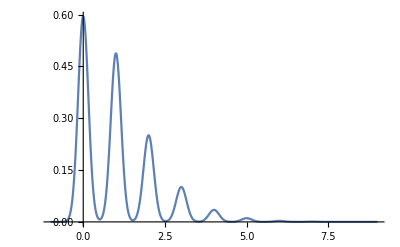

```mathematica
fcfPlot[
fcfList[
{(640/219475.6)^2, (580/219475.6)^2}, 
400
]
]
```

##### FCF tests

```mathematica
IdentityMatrix[3]
.RotationMatrix[π/6., {0, 0, 1}]
```

{{0.866025,-0.5,0.},{0.5,0.866025,0.},{0.,0.,1.}}

```mathematica
hoOvIntegrate[
{{0, 1, 0}, {0, 2, 0.}, {0,2, 0.}},
{{0, 1, 1}, {0, 2, 0.}, {0, 2, 0.}},
IdentityMatrix[3]
.RotationMatrix[π/6., {0, 0, 1}]
(*.RotationMatrix[-π/6., {0, 1, 0}]*)
(*.RotationMatrix[π/6., {1, 0, 0}]*)
]
```

0.749677

```mathematica
hoOvIntegrate[
{{0, 1, -.5}, {0, 1, 0.}, {0,3, 0.}},
{{2, 2, 0}, {0, 4, 0.}, {0, 5, 0.}},
IdentityMatrix[3]
.RotationMatrix[π/6., {0, 0, 1}]
.RotationMatrix[-π/6., {0, 1, 0}]
(*.RotationMatrix[π/6., {1, 0, 0}]*)
]
```

0.145714

```mathematica
hoOvIntegrate[
{{0, 1, 0}, {0, 1, 0.}, {0,3, 0.}},
{{2, 1, 0}, {0, 1, 0.}, {0, 3, 0.}},
IdentityMatrix[3]
(*.RotationMatrix[π/6., {0, 0, 1}]*)
.RotationMatrix[-π/6., {0, 1, 0}]
(*.RotationMatrix[π/6., {1, 0, 0}]*)(*//Transpose*),
False
]
```

-0.104518

```mathematica
IdentityMatrix[3]
.RotationMatrix[π/6., {0, 0, 1}]
.RotationMatrix[-π/6., {0, 1, 0}]
```

{{0.75,-0.5,-0.433013},{0.433013,0.866025,-0.25},{0.5,0.,0.866025}}

```mathematica
1.4142135623730951
```

```mathematica
0.05104821447767109/2
```

0.0255241

```mathematica
Tuples[Map[Range, {3, 3, 1}]]-1
```

{{0,0,0},{0,1,0},{0,2,0},{1,0,0},{1,1,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}

```mathematica
0.06330096580207173-0.04371557882305752
```

0.0195854

```mathematica
0.10451788007488536-0.0802644215981212
```

0.0242535

```mathematica
0.21402802153300873-0.19195452142674002
```

0.0220735

```mathematica
hoOvIntegrateBreakdown[
{{0, 1, 0}, {0, 1, 0.}, {0,50, 0.}},
{{2, 1, 0}, {0, 1, 0.}, {0, 50, 0.}},
IdentityMatrix[3]
.RotationMatrix[π/6., {0, 0, 1}]
.RotationMatrix[-π/6., {0, 1, 0}]
(*.RotationMatrix[π/6., {1, 0, 0}]*)//Transpose
][[2]][5]//Total
```

```mathematica
0.04596497-0.06104897877088497/1.4142135623730951(*50*)
```

0.00279682

```mathematica
(0.27523118-0.36675490392827964/1.4142135623730951)(*15*)
```

0.0158963

```mathematica
(0.56986589-0.7624559437546635/1.4142135623730951)(*8*)
```

0.0307281

```mathematica
(0.89643197-1.2055783754650922/1.4142135623730951) (*5*)
```

0.0439593

```mathematica
1.81693163-2.492413801425365/1.4142135623730951(*3*)
```

0.0545289

```mathematica
1.36191439-1.8480659423267976/1.4142135623730951(*2*)
```

0.0551344

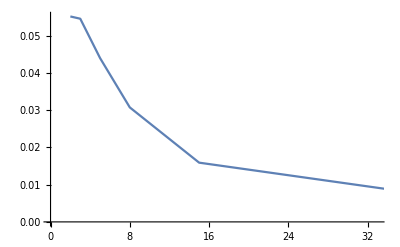

```mathematica
ListLinePlot[{
{2, 0.055134430100814535},
{3, 0.05452892948918331},
{5, 0.043959325456771725},
{8, 0.03072812181508855},
{15, 0.015896300398892727},
{50, 0.002796823126593663}
}
]
```

```mathematica
hoOvIntegrate[
{{0, 1, 0}, {0, 2, 0.}, {0,3, 0.}},
{{1, 1, 0}, {1, 2, 0.}, {0, 3, 0.}},
RotationMatrix[π/6., {0, 0, 1}]
]
```

0.146187

##### NH3 FCFs

```mathematica
nh3Dusch="-9.41763616e-01 -6.51566715e-06  7.26882561e-05 -2.85654353e-04 -9.83516227e-05 -3.36275436e-01
 3.88948784e-05  4.70308995e-01  7.92175674e-01  1.41790389e-01  8.68327092e-02 -3.47789835e-05
-1.78242057e-05  7.92325942e-01 -4.70309659e-01 -8.69618333e-02  1.41351819e-01  1.28046068e-04
 3.36275515e-01  2.45390518e-04  1.29601429e-05 -8.89461077e-04 -3.74225711e-04 -9.41763094e-01
 5.18232551e-05 -1.42655801e-01 -2.77442065e-01  7.55004756e-01  4.02904291e-01 -9.05231565e-04
-1.42616865e-04  2.76930985e-01 -1.42707882e-01  4.02901585e-01 -7.55190357e-01  4.71002802e-05"//ImportString[#, "Table"]&;
nh3ESCenter=" 5.08416035e+01  2.64547883e-02 -1.20861127e-02  1.92495731e-02  7.95952579e-03  2.00590167e+01"//ImportString[#, "Table"]&//First;
nh3GSFreqs="0.0048229  0.00747687 0.00747819 0.0154197  0.01598601 0.01598695"//ImportString[#, "Table"]&//First;
nh3ESFreqs=
"0.00022738 0.00443953 0.0044397  0.0098293  0.00983265 0.0111599"//ImportString[#, "Table"]&//First;
```

```mathematica
nh3States="[[0, 0, 0, 0, 0, 0],
                        [1, 0, 0, 0, 0, 0],
                        [2, 0, 0, 0, 0, 0],
                        [3, 0, 0, 0, 0, 0],
                        [0, 1, 0, 0, 0, 0],
                        [0, 0, 1, 0, 0, 0],
                        [0, 0, 0, 1, 0, 0],
                        [0, 0, 0, 0, 1, 0],
                        [0, 0, 0, 0, 0, 1]]"//ImportString[#, "JSON"]&;
```

```mathematica
Transpose@{
states[[1]],
nh3ESFreqs,
nh3ESCenter
}
```

{{0,0.00022738,50.8416},{0,0.00443953,0.0264548},{0,0.0044397,-0.0120861},{0,0.0098293,0.0192496},{0,0.00983265,0.00795953},{0,0.0111599,20.059}}

```mathematica
hoOvIntegrate[
{0, #, 0}&/@nh3GSFreqs,
Transpose@{
states[[5]],
nh3ESFreqs,
nh3ESCenter
},
nh3Dusch//Transpose
]^2
```

5.93123×10^-8

```mathematica
hoOvIntegrate[
{{0, 1, 0}, {0, 1, 0.}, {0,3, 0.}},
{{1, 2, -.5}, {0, 5, 0.}, {1, 7, 0.}},
IdentityMatrix[3]
.RotationMatrix[π/6., {0, 0, 1}]
.RotationMatrix[-π/6., {0, 1, 0}]
(*.RotationMatrix[π/6., {1, 0, 0}]*)//Transpose
]
```

-0.109804

```mathematica
nh3GSTF=ImportString["[-9.41763616e-01 -6.51566715e-06  7.26882561e-05 -2.85654353e-04 -9.83516227e-05 -3.36275436e-01]
 [ 3.88948784e-05  4.70308995e-01  7.92175674e-01  1.41790389e-01  8.68327092e-02 -3.47789835e-05]
 [-1.78242057e-05  7.92325942e-01 -4.70309659e-01 -8.69618333e-02  1.41351819e-01  1.28046068e-04]
 [ 3.36275515e-01  2.45390518e-04  1.29601429e-05 -8.89461077e-04 -3.74225711e-04 -9.41763094e-01]
 [ 5.18232551e-05 -1.42655801e-01 -2.77442065e-01  7.55004756e-01  4.02904291e-01 -9.05231565e-04]
 [-1.42616865e-04  2.76930985e-01 -1.42707882e-01  4.02901585e-01 -7.55190357e-01  4.71002802e-05]"];
```

```mathematica
nh3GSFreqs=
```

## Kenny Data

#### Raw Data

```mathematica
neutralFreqsStr="6:        94.13 cm**-1
   7:        94.47 cm**-1
   8:       111.27 cm**-1
   9:       221.46 cm**-1
  10:       233.53 cm**-1
  11:       236.75 cm**-1
  12:       240.22 cm**-1
  13:       248.14 cm**-1
  14:       248.71 cm**-1
  15:       268.68 cm**-1
  16:       290.51 cm**-1
  17:       290.67 cm**-1
  18:       395.21 cm**-1
  19:       451.82 cm**-1
  20:       452.03 cm**-1
  21:       537.95 cm**-1
  22:       589.17 cm**-1
  23:       589.43 cm**-1
  24:       592.64 cm**-1
  25:       593.95 cm**-1
  26:       594.74 cm**-1
  27:       661.11 cm**-1
  28:       735.43 cm**-1
  29:       735.68 cm**-1
  30:       746.24 cm**-1
  31:       758.66 cm**-1
  32:       786.20 cm**-1
  33:       786.49 cm**-1
  34:       791.11 cm**-1
  35:       791.37 cm**-1
  36:       841.15 cm**-1
  37:      1003.12 cm**-1
  38:      1003.19 cm**-1
  39:      1062.43 cm**-1
  40:      1075.67 cm**-1
  41:      1075.82 cm**-1
  42:      1171.58 cm**-1
  43:      1171.78 cm**-1
  44:      1176.47 cm**-1
  45:      1270.41 cm**-1
  46:      1304.99 cm**-1
  47:      1305.32 cm**-1
  48:      1391.88 cm**-1
  49:      1495.71 cm**-1
  50:      1496.30 cm**-1
  51:      1517.51 cm**-1
  52:      1565.59 cm**-1
  53:      1565.78 cm**-1
  54:      1570.78 cm**-1
  55:      1627.06 cm**-1
  56:      1627.43 cm**-1
  57:      1665.21 cm**-1
  58:      1687.27 cm**-1
  59:      1687.86 cm**-1
  60:      3603.24 cm**-1
  61:      3603.33 cm**-1
  62:      3604.87 cm**-1
  63:      3738.07 cm**-1
  64:      3738.27 cm**-1
  65:      3738.43 cm**-1";
neutralModesStr="              0          1          2          3          4          5    
      0       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      1       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      2       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      3       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      4       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      5       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      6       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      7       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      8       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      9       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     10       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     11       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     12       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     13       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     14       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     15       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     16       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     17       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     18       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     19       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     20       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     21       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     22       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     23       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     24       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     25       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     26       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     27       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     28       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     29       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     30       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     31       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     32       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     33       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     34       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     35       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     36       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     37       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     38       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     39       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     40       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     41       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     42       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     43       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     44       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     45       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     46       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     47       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     48       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     49       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     50       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     51       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     52       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     53       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     54       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     55       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     56       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     57       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     58       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     59       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     60       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     61       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     62       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     63       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     64       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     65       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
                  6          7          8          9         10         11    
      0       0.023847  -0.001568  -0.014038   0.000046   0.002779  -0.000202
      1      -0.220860   0.014916   0.128128  -0.000715  -0.025871   0.001661
      2      -0.052769   0.003849   0.030609  -0.000134  -0.006219   0.000345
      3      -0.000776   0.000261  -0.016703   0.000060   0.016083   0.000838
      4       0.003246  -0.002720   0.152056  -0.001986  -0.149802  -0.007382
      5       0.000922  -0.000216   0.036344  -0.000265  -0.035694  -0.001769
      6      -0.011482   0.022702  -0.013195  -0.000168   0.002585   0.000256
      7       0.099812  -0.204075   0.120493  -0.000826  -0.028309  -0.001306
      8       0.023818  -0.048375   0.028797  -0.000378  -0.006777  -0.000416
      9      -0.022408   0.027877  -0.007934  -0.037558  -0.004616   0.000079
     10       0.199287  -0.252727   0.072904   0.336432   0.039696  -0.000215
     11       0.047508  -0.059973   0.017404   0.079534   0.009649  -0.000042
     12      -0.008431   0.035210  -0.007944   0.038130  -0.005617  -0.000451
     13       0.073558  -0.310279   0.073703  -0.337691   0.045164   0.003914
     14       0.017511  -0.073915   0.017681  -0.080645   0.010392   0.000968
     15       0.002638   0.000254   0.001465  -0.000262  -0.002015   0.000197
     16      -0.021817   0.001923  -0.009924   0.003241   0.017552  -0.001183
     17      -0.004963   0.000879  -0.002236   0.000927   0.003932  -0.000434
     18      -0.013523  -0.032938  -0.008916  -0.039544  -0.005125  -0.000506
     19       0.120429   0.293432   0.081069   0.348404   0.045856   0.005698
     20       0.029159   0.071058   0.019268   0.083995   0.011327   0.001365
     21      -0.014602  -0.020319  -0.013749  -0.000629   0.002477   0.000511
     22       0.129321   0.182276   0.124742   0.000324  -0.025838  -0.004464
     23       0.031238   0.044131   0.029737   0.000128  -0.005931  -0.001145
     24      -0.026071  -0.024004  -0.008578   0.037384  -0.004609   0.000219
     25       0.234830   0.215853   0.077300  -0.347461   0.039677  -0.001482
     26       0.056523   0.051945   0.018285  -0.084117   0.009625  -0.000421
     27      -0.001310   0.001762   0.000901   0.000067  -0.001888   0.000033
     28       0.009404  -0.019711  -0.011265  -0.000910   0.016049  -0.000011
     29       0.001846  -0.005040  -0.003066  -0.000526   0.003718  -0.000139
     30       0.033767   0.005199  -0.009126  -0.037172  -0.004431  -0.000386
     31      -0.313392  -0.047771   0.082694   0.345792   0.041284   0.003105
     32      -0.075428  -0.011484   0.019585   0.082791   0.009833   0.000686
     33       0.033050  -0.010149  -0.009282   0.037129  -0.004774  -0.000251
     34      -0.303383   0.092068   0.085052  -0.342450   0.045946   0.000858
     35      -0.072195   0.022097   0.020429  -0.081460   0.010970   0.000148
     36      -0.001290  -0.002079   0.001092   0.000106  -0.001616  -0.000412
     37       0.011816   0.018193  -0.010357  -0.002168   0.014966   0.003813
     38       0.003017   0.004159  -0.002157  -0.000499   0.004017   0.000696
     39       0.035219  -0.001853   0.029700   0.001309   0.012059   0.009637
     40      -0.299646   0.027125  -0.255131  -0.002264  -0.091485  -0.079614
     41      -0.071419   0.006393  -0.060678  -0.000934  -0.022161  -0.018519
     42      -0.013131   0.027165   0.027720  -0.000069   0.004633   0.000351
     43       0.121238  -0.258710  -0.263752  -0.000105  -0.045204  -0.003219
     44       0.027896  -0.063490  -0.064082   0.000256  -0.011118  -0.000846
     45      -0.016505  -0.027383   0.027877   0.000861   0.011673  -0.008600
     46       0.159708   0.247547  -0.259570   0.000692  -0.097556   0.073819
     47       0.038395   0.057944  -0.060956   0.000873  -0.023283   0.018227
     48       0.035644  -0.025068   0.036366  -0.019078  -0.049244  -0.058423
     49      -0.301350   0.235944  -0.312998   0.183293   0.428764   0.488161
     50      -0.071665   0.056682  -0.074463   0.043918   0.101021   0.115148
     51       0.039362   0.023329   0.037393   0.026379  -0.051200  -0.059730
     52      -0.333361  -0.178148  -0.318197  -0.206616   0.427713   0.489040
     53      -0.079034  -0.044243  -0.074714  -0.051382   0.099715   0.116248
     54      -0.034449   0.019505   0.035017   0.020886  -0.016583  -0.002035
     55       0.314458  -0.189282  -0.331005  -0.191633   0.156511   0.019754
     56       0.074358  -0.046803  -0.080336  -0.045898   0.038041   0.004768
     57       0.006782   0.039137   0.034235  -0.021641  -0.016739  -0.002702
     58      -0.058618  -0.369578  -0.328296   0.197938   0.156999   0.025529
     59      -0.016500  -0.090717  -0.079701   0.048965   0.038242   0.006183
     60       0.000196  -0.041769   0.034664   0.019665  -0.051914   0.051502
     61      -0.000983   0.381825  -0.319541  -0.175067   0.482446  -0.469073
     62      -0.000070   0.090423  -0.075674  -0.041544   0.117155  -0.113561
     63      -0.037903  -0.015559   0.035788  -0.023553  -0.054286   0.053922
     64       0.345751   0.143381  -0.327528   0.213491   0.479122  -0.472885
     65       0.082526   0.034405  -0.078183   0.051281   0.115592  -0.112950
                 12         13         14         15         16         17    
      0       0.001015   0.000718   0.000515  -0.005619  -0.048144   0.015359
      1      -0.009512  -0.008695  -0.003713   0.049211   0.006662  -0.013370
      2      -0.002575  -0.002492  -0.000687   0.010890  -0.047241   0.067905
      3       0.004877  -0.002565   0.001205  -0.029887  -0.074754  -0.020855
      4      -0.043530   0.013573  -0.010349   0.274693  -0.001562  -0.014602
      5      -0.010700   0.003307  -0.002440   0.064614  -0.021391   0.073694
      6       0.000523  -0.002123   0.001007  -0.004973  -0.090676  -0.022692
      7      -0.003966   0.008618  -0.010148   0.049150  -0.007306  -0.007404
      8      -0.001045   0.002493  -0.002494   0.011498  -0.011309   0.025262
      9      -0.001087   0.037732   0.023746   0.007418  -0.056201  -0.023493
     10       0.011430  -0.347463  -0.219883  -0.064595  -0.015388  -0.008292
     11       0.002714  -0.081547  -0.052397  -0.015627   0.038838   0.020844
     12      -0.001173  -0.033050  -0.033761   0.007794  -0.057441  -0.004250
     13       0.009970   0.285673   0.297865  -0.065181   0.004383  -0.001762
     14       0.002388   0.067773   0.070902  -0.015355  -0.050991   0.000365
     15      -0.001179  -0.023232  -0.003903   0.003267   0.001239   0.027782
     16       0.009081   0.206752   0.033882  -0.031018   0.006730  -0.002533
     17       0.002148   0.049606   0.007840  -0.007782  -0.032113   0.019010
     18      -0.002498  -0.038606   0.021973   0.007345  -0.002096   0.010518
     19       0.020813   0.342692  -0.193750  -0.064793  -0.004253  -0.019841
     20       0.004762   0.082706  -0.046785  -0.016954   0.006506   0.073494
     21       0.001137  -0.001799  -0.000653  -0.004777  -0.036404  -0.040600
     22      -0.009191   0.006417   0.008959   0.049492  -0.005888  -0.023029
     23      -0.002528   0.001670   0.002191   0.010589   0.007633   0.077585
     24      -0.000459   0.041074  -0.012303   0.007906  -0.034926  -0.063357
     25       0.005844  -0.384684   0.114852  -0.064005  -0.004850  -0.013730
     26       0.001119  -0.092924   0.027810  -0.015874   0.008077   0.020877
     27       0.000548   0.013865  -0.018361   0.003339  -0.040083  -0.008782
     28      -0.004777  -0.131011   0.172170  -0.030985  -0.004702   0.003622
     29      -0.001292  -0.032017   0.041635  -0.007188   0.003138  -0.022327
     30      -0.000568   0.002100  -0.044836   0.006236  -0.058569   0.039842
     31       0.004176  -0.022004   0.418295  -0.064193  -0.001031  -0.001137
     32       0.000795  -0.005812   0.100656  -0.015728  -0.023122   0.019709
     33      -0.002243  -0.010745   0.043065   0.007306   0.004838  -0.013962
     34       0.021538   0.101261  -0.398054  -0.064972   0.009961  -0.017337
     35       0.004877   0.023866  -0.094797  -0.016134  -0.039644   0.061481
     36      -0.000875   0.009075   0.022004   0.003701   0.012014  -0.026085
     37       0.009725  -0.079776  -0.202689  -0.030793  -0.003577  -0.010049
     38       0.002216  -0.018684  -0.048799  -0.007682   0.021108   0.028849
     39      -0.003267   0.032138   0.003431   0.000462   0.176319   0.195918
     40       0.022457  -0.249172  -0.036149  -0.029254   0.050152   0.037745
     41       0.005338  -0.060400  -0.008431  -0.005544  -0.121254  -0.062485
     42       0.010048  -0.018643   0.024438   0.003660  -0.044637  -0.001134
     43      -0.096647   0.174969  -0.231334  -0.036548  -0.020513   0.066509
     44      -0.022148   0.042188  -0.055542  -0.004641   0.065372  -0.284320
     45      -0.001646  -0.008905  -0.026576   0.004471   0.236651  -0.094528
     46       0.017446   0.093667   0.252528  -0.027499  -0.012751  -0.007645
     47       0.004548   0.022720   0.059306  -0.007083   0.163706  -0.011216
     48       0.023519   0.038008   0.024298  -0.048717   0.361141   0.370886
     49      -0.204333  -0.280898  -0.223336   0.358752   0.041974   0.034611
     50      -0.048319  -0.066486  -0.053486   0.084063  -0.003530   0.050870
     51       0.024850   0.040212  -0.009180  -0.046923   0.181663   0.200736
     52      -0.208257  -0.314036   0.066301   0.357843   0.099919   0.090222
     53      -0.048811  -0.077191   0.017765   0.089354  -0.334836  -0.264077
     54      -0.064359   0.001009   0.022405  -0.038509   0.014822  -0.252208
     55       0.621616  -0.010617  -0.204473   0.395671  -0.024795   0.092524
     56       0.153584  -0.002934  -0.048511   0.102767   0.102032  -0.435207
     57      -0.066677  -0.021382   0.002221  -0.045326  -0.106190   0.255300
     58       0.619663   0.201457  -0.029021   0.394756  -0.036738   0.140872
     59       0.153307   0.048647  -0.005718   0.102490   0.094939  -0.407563
     60       0.020171  -0.025704  -0.020119  -0.036703   0.490718  -0.170418
     61      -0.176802   0.262712   0.193375   0.351632   0.042975  -0.022238
     62      -0.042783   0.062842   0.045121   0.084519   0.034120   0.028194
     63       0.021000   0.002136  -0.032160  -0.039085   0.226160  -0.091958
     64      -0.180690  -0.004371   0.298579   0.352651  -0.084679   0.016076
     65      -0.042710   0.002179   0.072421   0.085311   0.445069  -0.094415
                 18         19         20         21         22         23    
      0      -0.023522  -0.014830  -0.137278  -0.030159   0.068311  -0.086910
      1      -0.005360   0.037617  -0.006428   0.009538  -0.022784   0.024858
      2       0.011811  -0.163115  -0.037709  -0.054666   0.139166  -0.148348
      3       0.000048  -0.049406   0.028670  -0.000027   0.173170   0.050808
      4      -0.000450   0.001831   0.013124  -0.000323   0.006929   0.048298
      5       0.000045  -0.028984  -0.048327  -0.000290   0.050557  -0.177405
      6       0.000735  -0.161451   0.081842   0.062504   0.220595   0.056708
      7       0.006333  -0.028812  -0.018021   0.006255   0.018228   0.003394
      8      -0.026079   0.048443   0.110842   0.004046   0.009817   0.011508
      9      -0.096086  -0.275469  -0.014871   0.053084  -0.012778   0.136782
     10       0.001959  -0.023316  -0.030186   0.025982   0.040157   0.001071
     11      -0.053200  -0.028683   0.118125  -0.083267  -0.123871   0.042526
     12       0.098948  -0.147703   0.233636   0.048113   0.041678  -0.133306
     13       0.021102  -0.040618   0.009720  -0.016524  -0.011718  -0.032925
     14      -0.042221   0.098166   0.067812   0.089403   0.100635   0.086557
     15       0.099055   0.009124   0.203680   0.097876  -0.143805  -0.117047
     16       0.023099  -0.053064   0.012741  -0.031920  -0.024655  -0.035468
     17      -0.049160   0.226504   0.041542   0.180376   0.041452   0.092597
     18       0.092856   0.005461   0.184490   0.049205  -0.143566  -0.055992
     19       0.024100  -0.041441   0.056610  -0.016043  -0.033121   0.014650
     20      -0.053099   0.173612  -0.152791   0.087857   0.046548  -0.098193
     21       0.022828   0.101469   0.098858  -0.032796   0.026723   0.122987
     22      -0.001101  -0.005613   0.044990  -0.016723   0.017480   0.058550
     23       0.014556   0.070965  -0.146569   0.050446  -0.056814  -0.186747
     24      -0.009717   0.156793   0.072126  -0.101731   0.043568   0.104581
     25      -0.026971   0.030275   0.063683  -0.009714   0.034090  -0.011580
     26       0.105760  -0.052951  -0.234051  -0.006505  -0.121056   0.092755
     27      -0.003261   0.218729  -0.109581  -0.206508  -0.037813  -0.016558
     28      -0.026925   0.042025   0.029122  -0.019334   0.005877  -0.050501
     29       0.109393  -0.076269  -0.170738  -0.011268  -0.049218   0.204590
     30       0.003240   0.038088  -0.158595  -0.102394   0.079669  -0.080035
     31      -0.025158   0.043052   0.028957  -0.009957  -0.012105  -0.039744
     32       0.106530  -0.161528  -0.192182  -0.005213   0.076485   0.133861
     33      -0.089338  -0.135571  -0.111018   0.054218  -0.150530  -0.014038
     34       0.005923   0.042331  -0.023897   0.025765  -0.022851   0.028670
     35      -0.063507  -0.238859   0.047332  -0.082653  -0.020098  -0.111425
     36      -0.095697  -0.157912  -0.134599   0.108908  -0.172468   0.029569
     37       0.003799   0.008724  -0.062011   0.051868   0.003842  -0.011874
     38      -0.060314  -0.109165   0.197567  -0.168756  -0.095769   0.065871
     39      -0.111875   0.104642   0.102353   0.135098   0.004104   0.046112
     40      -0.026247  -0.043177  -0.017859  -0.043766   0.011342  -0.001728
     41       0.056186   0.232836   0.125815   0.249617  -0.048796   0.028744
     42       0.004081   0.266883  -0.140624  -0.285449  -0.060218  -0.014041
     43       0.030307   0.028730  -0.005450  -0.026628  -0.007065   0.007418
     44      -0.124649  -0.001981  -0.038665  -0.015548   0.005523  -0.038705
     45       0.107764  -0.025735  -0.160615   0.150090   0.021119  -0.041922
     46      -0.004585   0.003463  -0.075983   0.071528  -0.005844  -0.015396
     47       0.067963  -0.028202   0.247316  -0.233545   0.032966   0.044962
     48      -0.358812   0.183015  -0.000360   0.148379   0.242707   0.298826
     49      -0.019319  -0.049883  -0.019001  -0.055214   0.111096   0.053091
     50      -0.102591   0.284082   0.058860   0.258085   0.137132   0.210523
     51      -0.119148   0.107103   0.100236   0.136284   0.024818   0.061772
     52      -0.094464  -0.024004  -0.047646  -0.037715  -0.023690   0.006558
     53       0.341760   0.165166   0.259746   0.267554  -0.372385  -0.277640
     54      -0.245438   0.340079  -0.031044  -0.300455   0.018090  -0.378343
     55       0.043297   0.027940  -0.011929  -0.029354  -0.020954   0.027907
     56      -0.278745   0.041895   0.028963  -0.022534   0.051486  -0.263777
     57       0.261995   0.214097  -0.266134  -0.301049  -0.152252   0.360182
     58       0.090485   0.015825  -0.033938  -0.026793  -0.016665   0.089797
     59      -0.251336   0.025178   0.021475  -0.010404   0.052642  -0.224207
     60       0.363876   0.107564  -0.168122   0.162493   0.346576  -0.146284
     61       0.056737   0.036868  -0.074881   0.073705   0.288723  -0.121538
     62      -0.061763  -0.096391   0.253605  -0.243158  -0.091643   0.083321
     63       0.096991  -0.032044  -0.163398   0.153555   0.030875  -0.047471
     64      -0.074615  -0.032871  -0.077409   0.074687  -0.311958   0.093350
     65       0.352868   0.119750   0.266106  -0.249672   0.373575  -0.049634
                 24         25         26         27         28         29    
      0      -0.006789   0.004982  -0.001808  -0.194696   0.043695  -0.048084
      1       0.007070  -0.007534   0.009834  -0.043460  -0.397974   0.456412
      2      -0.009893   0.007413   0.000732   0.097567  -0.096204   0.110668
      3      -0.007211   0.011873   0.000431   0.000455   0.000879  -0.000148
      4       0.001142   0.000740   0.000553   0.000233  -0.000479   0.000072
      5      -0.007840   0.002404  -0.001963  -0.000051  -0.000939  -0.000375
      6      -0.008955   0.013537   0.000054   0.007716   0.022687   0.063659
      7      -0.004999   0.012856   0.001800   0.051127  -0.194539  -0.573985
      8      -0.001575   0.003161   0.000415  -0.216039  -0.047234  -0.136800
      9       0.002602   0.001979   0.001052   0.213837   0.005652  -0.016746
     10       0.026546  -0.017042   0.003851   0.051329  -0.029736   0.145403
     11       0.013941  -0.012533   0.001515  -0.118074  -0.007524   0.034140
     12      -0.005809   0.005032  -0.000561  -0.205397  -0.012942  -0.012713
     13      -0.009099  -0.032016  -0.011814   0.010912   0.111627   0.095358
     14      -0.004936  -0.000647  -0.002122  -0.140566   0.026327   0.022547
     15       0.003197  -0.010198  -0.001817   0.011185   0.024027  -0.027275
     16       0.002412  -0.004957   0.003761   0.003055  -0.208411   0.240772
     17       0.001097   0.001936   0.001685  -0.005424  -0.049576   0.057897
     18       0.004176  -0.013478  -0.002335   0.001828   0.012336   0.011722
     19       0.012836   0.026898   0.015360  -0.058135  -0.111297  -0.098064
     20      -0.002419   0.009444   0.002505   0.243158  -0.025340  -0.026429
     21       0.002528   0.002946   0.002590   0.187734  -0.066031  -0.013976
     22      -0.000158  -0.003883  -0.010612  -0.007434   0.594327   0.118239
     23      -0.002941  -0.006309  -0.004794   0.118536   0.144356   0.026713
     24       0.001841   0.004091  -0.002414   0.223127   0.014314  -0.006488
     25      -0.007819  -0.002594   0.032985   0.048376  -0.138976   0.047610
     26       0.007307  -0.008799   0.009053  -0.100995  -0.033227   0.011545
     27       0.001721  -0.002936   0.000146  -0.000424   0.010779   0.031939
     28      -0.003639   0.005345   0.000186  -0.003573  -0.103273  -0.298780
     29       0.007978  -0.000875   0.002385   0.012356  -0.025363  -0.072443
     30      -0.007121   0.004348   0.002882  -0.215971  -0.014525   0.006763
     31       0.003599   0.008069  -0.032711   0.006426   0.139960  -0.047440
     32       0.000893   0.008356  -0.006256  -0.124876   0.034122  -0.010401
     33       0.010490  -0.012042   0.000848  -0.017931  -0.003923   0.015646
     34      -0.027054   0.016220  -0.007920  -0.059099   0.027675  -0.145590
     35      -0.008044   0.002440  -0.002905   0.241096   0.003914  -0.034093
     36       0.009799  -0.011207   0.000924  -0.011391  -0.034785  -0.007516
     37      -0.000884  -0.002416  -0.005256   0.000385   0.312194   0.061150
     38       0.006988  -0.006378  -0.000226  -0.007022   0.074708   0.013973
     39       0.001464   0.000831   0.000738  -0.047526  -0.005887   0.008089
     40      -0.001211   0.001879  -0.001083  -0.011129   0.049830  -0.057436
     41       0.003012  -0.003486  -0.000247   0.023947   0.012007  -0.011882
     42       0.002814  -0.003525   0.000198   0.001524  -0.003218  -0.007254
     43       0.001198  -0.001881  -0.000199   0.012973   0.024671   0.071846
     44      -0.001268  -0.000126  -0.000533  -0.053041   0.005866   0.017785
     45      -0.003381   0.001330  -0.000948   0.045904   0.007170   0.001894
     46      -0.000225   0.000174   0.001129  -0.001948  -0.075135  -0.014507
     47      -0.000775   0.003347   0.000997   0.029333  -0.016020  -0.003268
     48       0.027435   0.086497   0.028795  -0.257490   0.011467   0.025234
     49      -0.270852  -0.588190  -0.223553   0.000094  -0.097599  -0.210334
     50      -0.064496  -0.132587  -0.051663  -0.107168  -0.022917  -0.048540
     51      -0.031421  -0.070919  -0.025996  -0.054687  -0.026320  -0.007445
     52       0.264339   0.596925   0.218350  -0.075161   0.216942   0.069274
     53       0.074340   0.118453   0.050080   0.263306   0.051191   0.021113
     54      -0.030765  -0.017668   0.064370  -0.207995   0.018605  -0.015084
     55       0.178737   0.162312  -0.640235   0.021097  -0.172590   0.154334
     56       0.032486   0.041901  -0.158482  -0.185505  -0.041472   0.038427
     57       0.037346   0.010256  -0.064077   0.218439  -0.026108  -0.002075
     58      -0.170697  -0.170935   0.640674   0.065128   0.231028   0.015332
     59      -0.052013  -0.039251   0.154141  -0.161374   0.056843   0.004443
     60      -0.084809   0.053697  -0.011111   0.265143   0.006374   0.024853
     61       0.598531  -0.291569   0.086746   0.037570  -0.050333  -0.222854
     62       0.153215  -0.078620   0.022212  -0.081956  -0.011167  -0.053901
     63       0.066209  -0.033696   0.008481   0.037214   0.013541  -0.021185
     64      -0.596455   0.292264  -0.080648  -0.049039  -0.129277   0.187040
     65      -0.161460   0.097079  -0.019256   0.273958  -0.029363   0.044359
                 30         31         32         33         34         35    
      0       0.138377  -0.028692   0.030737  -0.017336   0.164288   0.059602
      1      -0.053177   0.261866  -0.246881   0.170443   0.031590   0.027504
      2       0.255198   0.065166  -0.055960   0.036532  -0.023422  -0.114918
      3      -0.000523   0.021479  -0.002458   0.002777   0.057554   0.109400
      4       0.001971  -0.198826   0.001769   0.001132   0.030740  -0.002109
      5       0.000880  -0.047224  -0.007514   0.002144  -0.105640   0.058629
      6      -0.292657  -0.031562   0.006408   0.031142  -0.035585  -0.085544
      7      -0.030349   0.258177  -0.022725  -0.301041   0.040654  -0.025338
      8      -0.016360   0.062518  -0.016545  -0.068965  -0.170227   0.078117
      9      -0.294184  -0.010284  -0.009048  -0.021705   0.171448  -0.143105
     10      -0.041479   0.054520   0.218909   0.156931   0.027191  -0.038354
     11       0.037949   0.013825   0.043369   0.041064  -0.056557   0.108978
     12      -0.290105  -0.007481   0.010556  -0.020009  -0.210595   0.048955
     13      -0.016999   0.054194  -0.185673   0.194285   0.014035   0.002894
     14      -0.070545   0.013864  -0.049445   0.046059  -0.142203  -0.019361
     15       0.026480   0.049797  -0.053138   0.039806   0.091149   0.010197
     16      -0.005288  -0.440519   0.487733  -0.340539  -0.004235   0.038151
     17       0.051101  -0.103959   0.120292  -0.083970   0.005277  -0.080114
     18       0.106717  -0.005178   0.029545  -0.012575   0.040028  -0.013761
     19       0.075365   0.054188  -0.242622   0.105870  -0.005936  -0.065945
     20      -0.269963   0.008816  -0.066014   0.033283   0.067177   0.237515
     21       0.154392  -0.026888  -0.040308  -0.009196  -0.058800   0.159093
     22       0.074941   0.263572   0.269770   0.125389  -0.028970  -0.003726
     23      -0.240410   0.059885   0.063607   0.034010   0.065794   0.108675
     24       0.201597  -0.003045  -0.005774   0.033473  -0.106850   0.199882
     25       0.070413   0.052703  -0.078680  -0.256351  -0.011692   0.051485
     26      -0.210101   0.010809  -0.011678  -0.065210   0.007902  -0.114275
     27      -0.057722   0.046520  -0.003511  -0.065961  -0.034805  -0.076948
     28       0.000870  -0.437936   0.056278   0.597176   0.014117  -0.025651
     29      -0.001529  -0.104427   0.008040   0.145426  -0.083251   0.032957
     30       0.186349  -0.006124   0.003646   0.029407   0.217336   0.034839
     31      -0.035431   0.051660   0.028938  -0.266816  -0.006427  -0.008448
     32       0.230200   0.013533   0.008443  -0.062386   0.119416   0.069890
     33       0.089146  -0.004390  -0.031344  -0.005581  -0.026029   0.034924
     34      -0.055756   0.053467   0.259852   0.065175   0.027621   0.054796
     35       0.281850   0.017456   0.063567   0.008653  -0.152257  -0.195641
     36       0.029913   0.049607   0.053869   0.029393  -0.051082   0.075793
     37       0.018200  -0.443172  -0.540300  -0.249694  -0.012935  -0.013396
     38      -0.046612  -0.106275  -0.127015  -0.057714   0.067996   0.052009
     39       0.063622  -0.011599   0.018158  -0.010630   0.070056  -0.089578
     40      -0.021310   0.097620  -0.094994   0.066020  -0.016675   0.028482
     41       0.117423   0.023875  -0.009816   0.010074   0.115991  -0.177400
     42      -0.133424  -0.010603   0.007017   0.005912  -0.106136  -0.217503
     43      -0.013810   0.097795  -0.009936  -0.115177  -0.007577  -0.019473
     44      -0.007635   0.024068  -0.002769  -0.028407  -0.013003  -0.007674
     45       0.071440  -0.008801  -0.016894  -0.005203  -0.126870  -0.001701
     46       0.033240   0.099686   0.100544   0.047532  -0.061783  -0.002797
     47      -0.110925   0.020251   0.032479   0.011656   0.195991   0.018901
     48       0.076808  -0.006917   0.015082  -0.007194  -0.167120  -0.279835
     49      -0.018526   0.104069  -0.103297   0.003694  -0.005017   0.035512
     50       0.128632   0.028817  -0.013954  -0.007420  -0.030027  -0.302538
     51       0.065244  -0.011879   0.010957  -0.013915   0.064287  -0.098859
     52      -0.029616   0.102754  -0.037722   0.090432  -0.098096  -0.009980
     53       0.131343   0.016752   0.014369   0.017807   0.420672  -0.007798
     54      -0.148689  -0.015253   0.030798  -0.001332   0.153066  -0.377396
     55      -0.013813   0.101610  -0.063927  -0.077416  -0.017750  -0.014096
     56      -0.015614   0.022279  -0.004457  -0.021138   0.152470  -0.103381
     57      -0.147724  -0.006343  -0.016517   0.004478  -0.401977  -0.107901
     58      -0.016858   0.100903   0.045370  -0.084657  -0.077569   0.006458
     59      -0.002174   0.022386   0.020436  -0.022092   0.131710  -0.066961
     60       0.086216  -0.011120  -0.005031  -0.009117  -0.131530  -0.317399
     61       0.036218   0.104081   0.097836  -0.018008  -0.062201  -0.069471
     62      -0.120165   0.022445   0.025945   0.001900   0.203766   0.178726
     63       0.073848  -0.009370  -0.011770  -0.008978  -0.133636   0.010197
     64       0.033405   0.102675   0.041859   0.084730  -0.072699   0.073480
     65      -0.126515   0.022222   0.039352   0.010204   0.252178  -0.328286
                 36         37         38         39         40         41    
      0      -0.041777   0.025223   0.151624   0.031921  -0.023865  -0.049241
      1       0.380270  -0.017873   0.031529   0.007273  -0.010978   0.012017
      2       0.090742   0.086133  -0.064331  -0.016633   0.034501  -0.072025
      3       0.041613   0.039205   0.098736   0.000256   0.139537  -0.037828
      4      -0.374211  -0.019123   0.019459   0.000244   0.023316   0.028692
      5      -0.089225   0.097643  -0.035603  -0.000998  -0.033485  -0.137750
      6      -0.042403   0.030638   0.084141  -0.000966   0.085306  -0.027265
      7       0.381538  -0.032402   0.023515  -0.008598   0.005887  -0.011402
      8       0.090806   0.152617  -0.060194   0.036191   0.015604   0.034553
      9       0.020097   0.162868  -0.228164   0.026313  -0.101621  -0.004616
     10      -0.182273  -0.014256   0.010036  -0.010983  -0.007985  -0.012144
     11      -0.043069   0.136510  -0.149650   0.058689  -0.013843   0.049200
     12       0.021004  -0.289823  -0.038346  -0.030233  -0.083707   0.058120
     13      -0.182175  -0.073890  -0.004120  -0.016638  -0.016267  -0.002914
     14      -0.042979   0.171008  -0.000905   0.055608   0.029330   0.039853
     15      -0.026863   0.008277  -0.068521   0.046856   0.017894   0.009792
     16       0.229636   0.002127  -0.015431   0.010439   0.004082  -0.000912
     17       0.054887  -0.003667   0.034362  -0.023434  -0.012181   0.008448
     18       0.019981   0.308524   0.051123  -0.065275  -0.065991  -0.030679
     19      -0.181046   0.067156   0.005924  -0.005732  -0.010748  -0.023490
     20      -0.044104  -0.133140   0.000001  -0.007182   0.013762   0.083325
     21      -0.041717   0.085850   0.122705  -0.030784   0.012079   0.056603
     22       0.378787  -0.018539   0.015011   0.001583   0.017660   0.014661
     23       0.090698   0.115839  -0.005150  -0.020341  -0.067639  -0.034636
     24       0.019936   0.023116   0.001986  -0.034511  -0.061540   0.019911
     25      -0.181776  -0.031196  -0.073752   0.009277  -0.023170  -0.012707
     26      -0.043825   0.139214   0.305556  -0.053897   0.068073   0.061578
     27      -0.024691   0.002271  -0.000828  -0.001656  -0.011487   0.004285
     28       0.231466   0.017015  -0.007266  -0.012441   0.000554   0.005242
     29       0.056252  -0.070255   0.030479   0.051799  -0.007441  -0.021730
     30       0.019042  -0.006478   0.037499   0.037509  -0.060784   0.012229
     31      -0.182282   0.030014   0.078065   0.016094   0.000365  -0.020273
     32      -0.043527  -0.128058  -0.308303  -0.050175  -0.028720   0.090322
     33       0.019694  -0.168020   0.252417   0.065211  -0.040181   0.057371
     34      -0.182183   0.008026  -0.002273   0.007131  -0.011681  -0.013638
     35      -0.042734  -0.110305   0.125204   0.000123   0.030606   0.083583
     36      -0.025150  -0.053574  -0.039694  -0.045192   0.008732  -0.018148
     37       0.230084   0.001858   0.002169   0.001762  -0.002665  -0.001516
     38       0.054459  -0.033740  -0.025069  -0.028430   0.015816  -0.001825
     39       0.004053  -0.081966  -0.069288   0.079914   0.103538   0.004380
     40      -0.034120   0.030549  -0.010697   0.018995   0.022309   0.011170
     41      -0.008369  -0.168055   0.010223  -0.040037  -0.041835  -0.044692
     42       0.003902  -0.073133  -0.174599  -0.002620   0.038515  -0.008059
     43      -0.034547   0.007793  -0.022644  -0.021389   0.011753   0.025898
     44      -0.008431  -0.064103   0.016670   0.086967  -0.031570  -0.109984
     45       0.004004   0.013445  -0.114005  -0.076619   0.083057  -0.057531
     46      -0.034064   0.030150  -0.036751   0.003131   0.004434   0.009583
     47      -0.008493  -0.121517   0.102598  -0.048641   0.019549  -0.067108
     48       0.000909  -0.174320   0.212256  -0.288296  -0.381664  -0.114808
     49      -0.005706   0.034914  -0.021407   0.032893   0.040263   0.015839
     50      -0.001467  -0.236795   0.187931  -0.273517  -0.348022  -0.121638
     51       0.000410  -0.089449  -0.060875   0.067719   0.086728  -0.000607
     52      -0.004136   0.038541   0.073588  -0.085524  -0.116733  -0.017196
     53      -0.000753  -0.201428  -0.330114   0.383588   0.520617   0.071272
     54       0.000289   0.166340  -0.352848  -0.364901   0.197456   0.473393
     55      -0.005529  -0.003735  -0.016276  -0.005026   0.004811   0.003786
     56      -0.001694   0.089202  -0.085611  -0.139631   0.066632   0.192732
     57       0.001415  -0.376655  -0.118684   0.372659  -0.105195  -0.513192
     58      -0.004903  -0.060553  -0.008060   0.064022  -0.021312  -0.089319
     59      -0.001558   0.082794  -0.019626  -0.099724   0.041747   0.141907
     60       0.001899   0.292023   0.016071   0.302793  -0.268013   0.326325
     61      -0.004386   0.092846  -0.010146   0.086828  -0.072314   0.093817
     62      -0.001991  -0.268058   0.044184  -0.240120   0.194858  -0.261165
     63       0.000703   0.010285  -0.130035  -0.091329   0.097606  -0.070219
     64      -0.004166  -0.021707  -0.097136  -0.095200   0.098678  -0.085972
     65      -0.002195   0.104402   0.360253   0.373162  -0.386467   0.344575
                 42         43         44         45         46         47    
      0      -0.061474  -0.080599   0.103565  -0.171187   0.085432   0.151558
      1       0.009576   0.031784  -0.034211  -0.040023  -0.049734  -0.024621
      2      -0.067699  -0.170512   0.190138   0.088542   0.246645   0.172265
      3      -0.277214   0.376717   0.000462  -0.000442  -0.050250   0.019435
      4      -0.117082  -0.025317   0.002496  -0.000059  -0.000729   0.013827
      5       0.361593   0.280248  -0.010163  -0.000002  -0.020346  -0.048942
      6       0.117078  -0.176582  -0.213840   0.008994   0.324803  -0.112313
      7       0.006974  -0.020712  -0.020831   0.046543   0.037245   0.003832
      8       0.026391   0.003830  -0.012489  -0.190986  -0.002644  -0.069018
      9       0.046057   0.010469   0.160101   0.013690  -0.138919   0.012391
     10       0.031795  -0.000901  -0.038401  -0.033079  -0.076909   0.011205
     11      -0.112875   0.008819   0.237449   0.146368   0.259597  -0.041706
     12      -0.020044  -0.029537   0.175775  -0.024901  -0.100140   0.068751
     13       0.007308   0.024299   0.070997  -0.036494   0.046215  -0.025227
     14      -0.039651  -0.115643  -0.214448   0.140012  -0.242458   0.139005
     15      -0.087962   0.021287  -0.024675   0.199839  -0.034162  -0.067191
     16      -0.016644   0.014488   0.008437   0.047801   0.020558   0.008375
     17       0.024750  -0.049778  -0.048066  -0.100990  -0.102783  -0.068960
     18      -0.052587  -0.067047  -0.282897  -0.134408   0.057406  -0.157701
     19       0.004773   0.013161  -0.035617  -0.000380  -0.017491   0.039063
     20      -0.044836  -0.086469   0.015341  -0.062141   0.099358  -0.235336
     21       0.110951   0.030616   0.110109   0.165206  -0.026166  -0.188208
     22       0.054893   0.003678   0.053623  -0.006825   0.018523  -0.085590
     23      -0.175999  -0.001993  -0.171394   0.104226  -0.088669   0.269422
     24       0.079943  -0.094756   0.107796  -0.113268   0.005916   0.304564
     25       0.000990  -0.006581  -0.051345   0.010468   0.002128   0.022946
     26       0.031681  -0.015152   0.261073  -0.094190  -0.006286   0.042824
     27       0.019980  -0.033077   0.054930  -0.007764  -0.132979   0.045961
     28      -0.017881  -0.016665   0.005722  -0.054732  -0.014320  -0.003063
     29       0.081455   0.053771   0.000675   0.222008   0.000603   0.032740
     30       0.062735  -0.108262   0.124542   0.117630  -0.189939  -0.240816
     31       0.007299  -0.016230   0.073169   0.032402  -0.023510  -0.026485
     32      -0.001840   0.019172  -0.249096  -0.081447   0.013074   0.002283
     33       0.080937   0.021922  -0.285425   0.139691   0.154614   0.095023
     34       0.029929   0.004680  -0.020699   0.027052   0.066188   0.036706
     35      -0.088737  -0.009131  -0.043060  -0.049542  -0.207981  -0.111324
     36       0.013269   0.086495  -0.030431  -0.193338   0.017030   0.079491
     37       0.009770  -0.002825  -0.014395   0.007614  -0.007901   0.035097
     38      -0.035166   0.051368   0.045047  -0.122002   0.040829  -0.110735
     39       0.090628  -0.003632   0.057245  -0.046889  -0.020988   0.102577
     40       0.012831  -0.018916  -0.019232  -0.011646  -0.026257   0.005938
     41      -0.008420   0.077097   0.108480   0.024425   0.100263   0.025385
     42      -0.041165   0.061748  -0.124946   0.002329   0.100738  -0.032189
     43       0.014720   0.018533  -0.012167   0.013154   0.017414   0.020218
     44      -0.078453  -0.049168  -0.004630  -0.052640  -0.027838  -0.097843
     45      -0.031780  -0.082799   0.067581   0.044635  -0.077612  -0.071464
     46      -0.018460   0.001965   0.031752  -0.001789   0.008474  -0.025707
     47       0.063348  -0.046466  -0.103039   0.028182  -0.071610   0.075243
     48      -0.257886   0.204587   0.146490   0.241158   0.250352  -0.057091
     49       0.024841  -0.026867  -0.023618  -0.021022  -0.037181   0.011441
     50      -0.224988   0.212294   0.175264   0.202052   0.278725  -0.072186
     51       0.077644   0.005524   0.063017  -0.033007  -0.013391   0.097346
     52      -0.095870   0.020072  -0.042155   0.069789   0.004013  -0.078353
     53       0.431491  -0.080330   0.205149  -0.302354  -0.025418   0.370330
     54       0.267752   0.325587  -0.228765   0.287475   0.303299   0.214198
     55      -0.000282   0.006945  -0.009453  -0.001114   0.009601   0.008931
     56       0.119656   0.113722  -0.059653   0.130774   0.091821   0.057355
     57      -0.412567  -0.141714  -0.212491  -0.292035   0.109404  -0.364887
     58      -0.069704  -0.028851  -0.029905  -0.055260   0.018391  -0.054375
     59       0.105894   0.057032   0.029319   0.098775  -0.026301   0.064365
     60      -0.103234   0.333945   0.152539  -0.249190   0.252560  -0.122241
     61      -0.035034   0.092678   0.053360  -0.063862   0.083296  -0.038328
     62       0.103448  -0.253993  -0.155504   0.171745  -0.240325   0.107278
     63      -0.036029  -0.097090   0.080034   0.051620  -0.088540  -0.084092
     64      -0.020395  -0.106375   0.058241   0.072108  -0.067996  -0.070472
     65       0.070542   0.421775  -0.212082  -0.296948   0.249970   0.263016
                 48         49         50         51         52         53    
      0      -0.105078  -0.048994   0.007729   0.275553   0.001975   0.040476
      1       0.035402   0.001234   0.013196   0.062565  -0.011192  -0.002455
      2      -0.195858  -0.027715  -0.051632  -0.137148   0.048091   0.028573
      3      -0.000092  -0.000874   0.003579  -0.000262  -0.089566   0.026234
      4       0.000031  -0.000915   0.000162  -0.000114  -0.003295   0.023768
      5       0.000267   0.003096   0.001095   0.000138  -0.027846  -0.087196
      6       0.222582   0.014479  -0.063006  -0.009128   0.060319  -0.013768
      7       0.022062  -0.008508  -0.008610  -0.073444   0.007658   0.005379
      8       0.011870   0.042500   0.006835   0.305157  -0.003788  -0.029257
      9      -0.067794   0.002382   0.040289   0.110382  -0.094473  -0.028528
     10      -0.021539  -0.016627   0.008856   0.024744   0.031540  -0.009450
     11       0.059255   0.071212  -0.018528  -0.052826  -0.177473   0.026530
     12      -0.063398  -0.024181   0.031095  -0.106756  -0.079419   0.074298
     13       0.008676  -0.015052  -0.008966   0.003676  -0.047056   0.021937
     14      -0.066545   0.051667   0.052611  -0.066440   0.159579  -0.056409
     15      -0.098414  -0.037869  -0.151920   0.229444   0.232531  -0.276913
     16       0.031529   0.044731   0.015249   0.053473   0.068237  -0.051286
     17      -0.180614  -0.206313  -0.137801  -0.113996  -0.174319   0.081327
     18      -0.020653   0.029873   0.057321  -0.006561  -0.092572   0.179349
     19       0.019254  -0.009775   0.004386  -0.029946  -0.017005   0.013289
     20      -0.089312   0.054870   0.009121   0.120730   0.027023   0.028952
     21      -0.117419   0.042064   0.026101  -0.264406  -0.017150  -0.040210
     22      -0.056996   0.015023  -0.005721   0.011036   0.005381  -0.015275
     23       0.183320  -0.042886   0.035975  -0.166664  -0.030138   0.045536
     24       0.090581  -0.035552   0.060096   0.108619   0.040571  -0.094790
     25       0.014487  -0.009341  -0.003499   0.025390   0.005521   0.032295
     26      -0.018850   0.022614   0.041406  -0.055991  -0.004568  -0.176623
     27       0.205256   0.068928  -0.270153  -0.006583  -0.075339   0.005357
     28       0.019128   0.028261  -0.020071  -0.061481  -0.031380  -0.093403
     29       0.011163  -0.086692  -0.036379   0.252083   0.096832   0.389600
     30       0.088593   0.002438   0.070754  -0.106929   0.086386   0.074662
     31       0.002650  -0.009196   0.012102   0.004524   0.026717   0.043962
     32       0.028806   0.039375  -0.018820  -0.066734  -0.072664  -0.149523
     33      -0.026045  -0.056166   0.036237  -0.001053  -0.166932  -0.114656
     34      -0.023378  -0.017409  -0.001141  -0.028973  -0.011563  -0.018834
     35       0.086564   0.047245   0.021470   0.121144  -0.027648   0.026772
     36      -0.109839   0.118715  -0.120071  -0.221485   0.323871   0.130103
     37      -0.052687   0.068808  -0.016720   0.008888  -0.018577   0.014460
     38       0.170775  -0.234074   0.014582  -0.139402   0.227862  -0.000205
     39       0.049129   0.000521   0.030296  -0.062838  -0.050709   0.032777
     40      -0.015740  -0.008636  -0.001016  -0.014847  -0.007311   0.012542
     41       0.090263   0.036445   0.019176   0.031444   0.005292  -0.036457
     42      -0.102893  -0.011597   0.043558   0.002156  -0.024140   0.008154
     43      -0.009588  -0.006787   0.002726   0.017063   0.001825   0.016274
     44      -0.005639   0.022959   0.007970  -0.069600  -0.017932  -0.063548
     45       0.054819  -0.016955   0.026944   0.060637  -0.058516  -0.001848
     46       0.026244  -0.011354   0.002397  -0.002455   0.000502   0.006963
     47      -0.085143   0.039382   0.002600   0.038356  -0.029087  -0.030185
     48       0.236722   0.352510   0.242268   0.177905   0.352988   0.051938
     49      -0.023753  -0.020475  -0.008079  -0.022931  -0.020271   0.011933
     50       0.218791   0.262926   0.158056   0.181049   0.258945  -0.018036
     51       0.050686  -0.003619   0.020954  -0.051976  -0.046338   0.017045
     52      -0.069956  -0.072876  -0.096937   0.052985  -0.011319  -0.098708
     53       0.313928   0.301603   0.413235  -0.244909   0.028341   0.420782
     54      -0.300350  -0.194427   0.419240   0.238760   0.335375   0.195486
     55      -0.002395   0.001639  -0.014187   0.005801  -0.014834   0.006641
     56      -0.119949  -0.091244   0.238069   0.081522   0.206261   0.060144
     57      -0.307210  -0.021637   0.474957  -0.247362   0.208258  -0.335879
     58      -0.054156  -0.008759   0.100126  -0.040278   0.053687  -0.063196
     59       0.087200   0.025911  -0.202615   0.057610  -0.130122   0.112834
     60       0.253112  -0.442191   0.054475  -0.188945   0.295696  -0.228679
     61       0.073130  -0.109207   0.009688  -0.057688   0.078328  -0.047299
     62      -0.193918   0.257371  -0.013378   0.160973  -0.202518   0.087266
     63       0.070522  -0.035177   0.035073   0.067365  -0.060047  -0.016423
     64       0.080478  -0.111942   0.057173   0.062790  -0.045773  -0.093993
     65      -0.309244   0.455186  -0.227650  -0.239669   0.175789   0.387283
                 54         55         56         57         58         59    
      0       0.039842  -0.027189   0.085572   0.036711  -0.315338   0.250333
      1      -0.013239  -0.011774   0.016978  -0.009048  -0.081390   0.044002
      2       0.073551   0.037081  -0.032336   0.054553   0.197949  -0.070477
      3       0.000146  -0.001432  -0.023120  -0.001791   0.066146  -0.128270
      4       0.000077   0.005139  -0.002727  -0.000350   0.036833   0.002049
      5      -0.000255  -0.022178   0.000705   0.000708  -0.124019  -0.067984
      6      -0.083963  -0.000769   0.024428  -0.064477  -0.040410   0.049915
      7      -0.008098  -0.023260   0.004533  -0.005642  -0.100041  -0.040801
      8      -0.005041   0.097600  -0.007689  -0.006298   0.402430   0.195238
      9       0.021921   0.014976  -0.002172   0.019129   0.033964   0.007584
     10       0.018621   0.014834  -0.009439   0.015687   0.039494   0.017386
     11      -0.068351  -0.055687   0.038933  -0.057419  -0.150692  -0.069801
     12       0.017901  -0.011234   0.002475   0.015742  -0.017541  -0.016455
     13      -0.014815   0.013844   0.006969  -0.012888   0.033813   0.015758
     14       0.070771  -0.063406  -0.028039   0.061552  -0.150285  -0.074020
     15      -0.038657   0.062267   0.004637  -0.073666  -0.059858  -0.039465
     16       0.011979  -0.015103  -0.012924   0.024193   0.007950   0.020893
     17      -0.069208   0.092916   0.056328  -0.136610  -0.062314  -0.106266
     18       0.050971  -0.049893  -0.020806   0.041682  -0.006173  -0.130130
     19      -0.007379   0.003951   0.003995  -0.006414   0.002737   0.012995
     20       0.054627  -0.039807  -0.026276   0.046281  -0.014070  -0.114252
     21       0.044259   0.039371   0.077791   0.038043  -0.000740   0.389801
     22       0.021375  -0.006957   0.000363   0.016775  -0.016315  -0.015055
     23      -0.068594   0.046813   0.034003  -0.052272   0.067989   0.241215
     24      -0.071858  -0.010767  -0.064967  -0.063152  -0.009871  -0.158412
     25      -0.002379  -0.001811  -0.000119  -0.002266   0.001683  -0.001251
     26      -0.022691   0.002637  -0.028819  -0.019137  -0.011257  -0.066891
     27       0.080437   0.011701   0.121994   0.157208   0.064378  -0.131169
     28       0.007309   0.007133   0.010899   0.014770  -0.000079  -0.015105
     29       0.005380  -0.024379   0.008849   0.008379   0.028612   0.004701
     30      -0.072442  -0.001500  -0.067219  -0.065089   0.131190  -0.094088
     31      -0.011134  -0.001985  -0.012201  -0.010018   0.024843  -0.015782
     32       0.013933   0.007612   0.020609   0.012555  -0.044594   0.023335
     33       0.053199   0.047270  -0.031402   0.043509   0.112497  -0.079965
     34       0.017424   0.012085  -0.010419   0.014431   0.032979  -0.020932
     35      -0.048780  -0.029323   0.029505  -0.040831  -0.087222   0.051384
     36      -0.041346  -0.065277   0.020653  -0.082769   0.072678   0.020198
     37      -0.020135  -0.024485   0.018666  -0.039353   0.033681  -0.003085
     38       0.064854   0.074471  -0.070080   0.128905  -0.109087   0.022542
     39      -0.017229  -0.054050  -0.020443   0.051934   0.036144   0.056256
     40       0.005598   0.016305   0.008806  -0.016677  -0.013245  -0.017136
     41      -0.032199  -0.095607  -0.047290   0.095899   0.073509   0.099511
     42       0.036580  -0.010991  -0.120619  -0.110104  -0.064251   0.130313
     43       0.003413  -0.002217  -0.011063  -0.010209  -0.006785   0.011709
     44       0.001825   0.004356  -0.006955  -0.005980  -0.000031   0.008732
     45      -0.019288   0.054805  -0.033885   0.058670  -0.072519   0.008101
     46      -0.009160   0.025061  -0.018077   0.028142  -0.034836   0.002266
     47       0.029797  -0.079814   0.060154  -0.091091   0.113347  -0.005777
     48       0.339713   0.455313   0.198915  -0.341968  -0.226117  -0.306285
     49      -0.005461   0.000657   0.002066  -0.005550  -0.007142  -0.008825
     50       0.195847   0.229915   0.093509  -0.151821  -0.084924  -0.119802
     51      -0.028579  -0.069422  -0.028725   0.067873   0.051608   0.078575
     52      -0.093943  -0.120021  -0.060228   0.091643   0.058611   0.083250
     53       0.381018   0.475761   0.241257  -0.356042  -0.222068  -0.312681
     54      -0.323409   0.021980   0.433121   0.284828   0.135246  -0.272497
     55       0.020243  -0.003647  -0.036604  -0.029391  -0.017711   0.033733
     56      -0.222288   0.024322   0.337531   0.243720   0.131207  -0.255713
     57      -0.337365   0.057923   0.449483   0.298930   0.141387  -0.287835
     58      -0.081372   0.013493   0.117598   0.083036   0.041213  -0.086313
     59       0.187098  -0.030255  -0.289080  -0.212346  -0.108041   0.229358
     60       0.348926  -0.424492   0.285357  -0.355676   0.381284  -0.021135
     61       0.076229  -0.087173   0.057022  -0.068104   0.067508  -0.004866
     62      -0.156125   0.161980  -0.101480   0.113983  -0.101135   0.008149
     63      -0.004728   0.036202  -0.020398   0.045957  -0.067860   0.008053
     64       0.090249  -0.100235   0.076481  -0.084017   0.085697  -0.006029
     65      -0.378402   0.429990  -0.325633   0.367084  -0.384419   0.029666
                 60         61         62         63         64         65    
      0       0.000801   0.000437  -0.000079   0.000012  -0.000096   0.000051
      1       0.000205   0.000028   0.000010  -0.000017  -0.000000  -0.000021
      2      -0.000513   0.000081  -0.000084   0.000073  -0.000041   0.000114
      3      -0.000213  -0.000238   0.000004  -0.000015   0.000044   0.000007
      4      -0.000076   0.000025   0.000005   0.000001   0.000004   0.000011
      5       0.000225  -0.000214  -0.000013  -0.000013   0.000005  -0.000041
      6       0.000212   0.000195   0.000118   0.000057  -0.000152  -0.000022
      7       0.000201  -0.000135   0.000000   0.000013  -0.000011  -0.000017
      8      -0.000757   0.000660   0.000048  -0.000021  -0.000035   0.000060
      9       0.000045  -0.000042   0.000123  -0.000028   0.000045  -0.000002
     10      -0.000229   0.000091  -0.000084  -0.000080   0.000035  -0.000003
     11       0.001002  -0.000405   0.000425   0.000327  -0.000124   0.000009
     12      -0.000076   0.000087   0.000159  -0.000019   0.000029   0.000010
     13      -0.000135   0.000222   0.000134  -0.000043  -0.000067  -0.000015
     14       0.000531  -0.000886  -0.000487   0.000171   0.000309   0.000070
     15       0.000354  -0.000372  -0.000543   0.000459   0.000850   0.000280
     16      -0.000005   0.000180   0.000187   0.000106   0.000203   0.000063
     17       0.000175  -0.000879  -0.001003  -0.000216  -0.000423  -0.000121
     18       0.000110  -0.000947  -0.000496  -0.000156  -0.000221  -0.000061
     19      -0.000008   0.000011  -0.000023   0.000006   0.000017   0.000013
     20       0.000085  -0.000498  -0.000150  -0.000099  -0.000171  -0.000080
     21       0.000300   0.000831  -0.000059   0.000046  -0.000065  -0.000075
     22       0.000063  -0.000050  -0.000033  -0.000005  -0.000016  -0.000038
     23      -0.000128   0.000579   0.000114   0.000046   0.000043   0.000120
     24      -0.000417  -0.000770   0.000324  -0.000116  -0.000054   0.000292
     25       0.000023   0.000059  -0.000055   0.000007   0.000005   0.000001
     26      -0.000285  -0.000590   0.000365  -0.000081  -0.000050   0.000133
     27      -0.000628  -0.000824   0.001115  -0.000005  -0.000026   0.000030
     28      -0.000016  -0.000118   0.000103  -0.000086  -0.000069   0.000251
     29      -0.000218   0.000116   0.000067   0.000354   0.000266  -0.001013
     30      -0.000698  -0.000581   0.000360   0.000105   0.000106  -0.000298
     31      -0.000179  -0.000143   0.000119   0.000029   0.000018  -0.000056
     32       0.000435   0.000335  -0.000338  -0.000073  -0.000036   0.000106
     33      -0.001012  -0.000025  -0.000447   0.000282  -0.000084   0.000022
     34      -0.000204  -0.000001  -0.000063   0.000070  -0.000027   0.000012
     35       0.000406  -0.000010   0.000070  -0.000164   0.000073  -0.000043
     36      -0.000516   0.000318  -0.000559  -0.000897   0.000388  -0.000107
     37      -0.000241   0.000039  -0.000249   0.000030  -0.000014  -0.000001
     38       0.000901  -0.000040   0.000885  -0.000556   0.000247  -0.000051
     39      -0.006531   0.019043   0.015312   0.030222   0.065738   0.023822
     40       0.001938  -0.005737  -0.004606   0.007257   0.015780   0.005724
     41      -0.011650   0.034340   0.027569  -0.015279  -0.033196  -0.012057
     42       0.026460   0.033242  -0.030535  -0.000718  -0.000587   0.002597
     43       0.002398   0.003035  -0.002781  -0.005387  -0.004658   0.019691
     44       0.001563   0.001872  -0.001758   0.021795   0.018849  -0.079662
     45       0.022796  -0.004382   0.015237  -0.064909   0.033437  -0.009847
     46       0.011150  -0.002117   0.007448   0.002637  -0.001355   0.000405
     47      -0.035003   0.006619  -0.023384  -0.041147   0.021185  -0.006265
     48      -0.094975   0.279628   0.223097  -0.147638  -0.320855  -0.116479
     49      -0.045696   0.134508   0.107361  -0.071609  -0.155600  -0.056471
     50       0.145727  -0.428932  -0.342410   0.229206   0.498046   0.180737
     51       0.181646  -0.533260  -0.425851  -0.275161  -0.598638  -0.216758
     52       0.019954  -0.058553  -0.046732  -0.029914  -0.065095  -0.023571
     53       0.009371  -0.027590  -0.022116  -0.015652  -0.033957  -0.012294
     54      -0.184879  -0.232326   0.212172   0.094955   0.081921  -0.346713
     55      -0.090512  -0.113754   0.103833   0.046058   0.039730  -0.168214
     56       0.291622   0.366523  -0.334525  -0.148041  -0.127711   0.540748
     57      -0.167064  -0.209655   0.191606  -0.084968  -0.073597   0.310464
     58       0.058592   0.073503  -0.067135   0.029320   0.025413  -0.107203
     59      -0.312210  -0.391711   0.357826  -0.156824  -0.135923   0.573332
     60       0.275652  -0.052223   0.182926   0.293646  -0.151185   0.044716
     61      -0.091153   0.017281  -0.060530  -0.098916   0.050914  -0.015045
     62       0.501140  -0.094996   0.332761   0.540244  -0.278093   0.082194
     63      -0.578897   0.110195  -0.384425   0.614307  -0.316447   0.093053
     64      -0.057638   0.010966  -0.038288   0.062102  -0.031979   0.009406
     65      -0.035994   0.006875  -0.023815   0.035144  -0.018149   0.005326";
```

```mathematica
anionFreqStr="   6:        98.92 cm**-1
   7:        99.57 cm**-1
   8:       110.72 cm**-1
   9:       186.16 cm**-1
  10:       260.08 cm**-1
  11:       260.27 cm**-1
  12:       261.34 cm**-1
  13:       262.57 cm**-1
  14:       274.12 cm**-1
  15:       357.33 cm**-1
  16:       377.16 cm**-1
  17:       377.85 cm**-1
  18:       427.26 cm**-1
  19:       438.85 cm**-1
  20:       439.02 cm**-1
  21:       502.41 cm**-1
  22:       502.95 cm**-1
  23:       518.01 cm**-1
  24:       557.33 cm**-1
  25:       591.18 cm**-1
  26:       591.27 cm**-1
  27:       660.86 cm**-1
  28:       663.13 cm**-1
  29:       667.48 cm**-1
  30:       668.29 cm**-1
  31:       702.42 cm**-1
  32:       702.80 cm**-1
  33:       728.79 cm**-1
  34:       738.34 cm**-1
  35:       739.06 cm**-1
  36:       770.38 cm**-1
  37:       951.76 cm**-1
  38:       952.08 cm**-1
  39:      1018.66 cm**-1
  40:      1018.92 cm**-1
  41:      1074.71 cm**-1
  42:      1075.19 cm**-1
  43:      1122.60 cm**-1
  44:      1132.85 cm**-1
  45:      1246.85 cm**-1
  46:      1247.49 cm**-1
  47:      1293.95 cm**-1
  48:      1294.02 cm**-1
  49:      1307.84 cm**-1
  50:      1411.19 cm**-1
  51:      1449.95 cm**-1
  52:      1450.32 cm**-1
  53:      1520.70 cm**-1
  54:      1553.19 cm**-1
  55:      1572.33 cm**-1
  56:      1572.77 cm**-1
  57:      1611.68 cm**-1
  58:      1612.05 cm**-1
  59:      1614.98 cm**-1
  60:      3517.70 cm**-1
  61:      3518.31 cm**-1
  62:      3519.98 cm**-1
  63:      3639.16 cm**-1
  64:      3639.46 cm**-1
  65:      3640.93 cm**-1
";
anionModesStr="                  0          1          2          3          4          5    
      0       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      1       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      2       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      3       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      4       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      5       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      6       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      7       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      8       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
      9       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     10       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     11       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     12       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     13       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     14       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     15       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     16       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     17       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     18       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     19       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     20       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     21       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     22       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     23       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     24       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     25       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     26       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     27       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     28       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     29       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     30       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     31       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     32       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     33       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     34       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     35       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     36       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     37       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     38       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     39       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     40       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     41       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     42       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     43       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     44       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     45       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     46       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     47       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     48       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     49       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     50       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     51       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     52       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     53       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     54       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     55       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     56       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     57       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     58       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     59       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     60       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     61       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     62       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     63       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     64       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
     65       0.000000   0.000000   0.000000   0.000000   0.000000   0.000000
                  6          7          8          9         10         11    
      0       0.025088   0.005477   0.015624  -0.024554   0.008342  -0.056224
      1      -0.209178  -0.100840  -0.126159   0.065069   0.014989   0.023728
      2      -0.051122  -0.021127  -0.026783  -0.018414  -0.041216  -0.082192
      3       0.016445  -0.011365   0.023189  -0.075247   0.034293  -0.038806
      4       0.001304  -0.023530  -0.205855   0.702094   0.014081   0.005117
      5       0.014120   0.011470  -0.049511   0.165074  -0.035642  -0.035096
      6      -0.020239   0.016123   0.009267   0.030800   0.070382  -0.078136
      7       0.183922  -0.150103  -0.118791   0.062895   0.020120  -0.009695
      8       0.047891  -0.030368  -0.028509   0.016461  -0.015635  -0.024943
      9      -0.047463   0.015463  -0.000331   0.058702   0.029397  -0.056769
     10       0.276653  -0.127993  -0.049868  -0.175323   0.066869   0.057631
     11       0.061828  -0.026373  -0.008678  -0.054277  -0.010733   0.055535
     12      -0.027891   0.041457  -0.000838   0.056932   0.048933  -0.036749
     13       0.192413  -0.234378  -0.044644  -0.180129  -0.083688  -0.038002
     14       0.049854  -0.057264  -0.014125  -0.028753   0.022511  -0.041653
     15       0.003910   0.002684  -0.000605   0.012783   0.000308  -0.014545
     16      -0.021281  -0.007480   0.007593  -0.066236  -0.015964  -0.041114
     17      -0.000477  -0.001059   0.001609  -0.002875  -0.017342  -0.043106
     18       0.000648  -0.019167   0.007484   0.010612  -0.015013   0.012261
     19      -0.031924   0.299862  -0.075034  -0.188640   0.039198  -0.102634
     20      -0.000660   0.057343  -0.023486  -0.002958  -0.068684  -0.029493
     21       0.002472  -0.023124   0.017272  -0.027245   0.061369  -0.012355
     22       0.030571   0.216794  -0.139451   0.051030   0.014593   0.003281
     23       0.010673   0.049028  -0.036138   0.046475  -0.084748  -0.033182
     24      -0.005501  -0.025496   0.013496  -0.012663   0.069301   0.013650
     25       0.108963   0.282523  -0.072345  -0.189742   0.020544   0.111283
     26       0.016026   0.050752  -0.019201  -0.018289  -0.019509   0.021580
     27       0.002214  -0.001207  -0.000759  -0.006740   0.030437  -0.033296
     28       0.018301  -0.012404   0.008588  -0.067668  -0.018649   0.044040
     29       0.003612  -0.004165   0.001801  -0.015795  -0.007558   0.005855
     30       0.025474   0.014127   0.011306  -0.008978  -0.022356  -0.066366
     31      -0.241563  -0.180071  -0.052819  -0.180111  -0.088534   0.024746
     32      -0.069177  -0.055599  -0.009155  -0.071034  -0.030729  -0.022024
     33       0.020670   0.004613   0.005713   0.013382  -0.008542   0.023027
     34      -0.294905  -0.055591  -0.060428  -0.171304   0.078752  -0.041843
     35      -0.084069  -0.009355  -0.008288  -0.082179   0.001533  -0.087406
     36      -0.001618  -0.005081  -0.000925   0.013392   0.017690   0.000797
     37       0.002521   0.022183   0.007618  -0.060122   0.049707   0.003349
     38       0.000511   0.009749   0.001932  -0.025330  -0.022963  -0.009851
     39       0.029672   0.000895  -0.022031   0.002122  -0.256070   0.049119
     40      -0.254816  -0.087761   0.246249   0.102965  -0.029333   0.089081
     41      -0.062953  -0.016648   0.065365   0.044183   0.114465  -0.070208
     42      -0.024068   0.016005  -0.035920  -0.035548   0.028243  -0.037840
     43       0.212283  -0.146276   0.255042   0.106617  -0.012361  -0.106451
     44       0.055678  -0.025742   0.059173   0.021837   0.225696   0.174857
     45       0.002955  -0.031581  -0.021157  -0.000736  -0.014349   0.249433
     46       0.029797   0.289274   0.230207   0.113872  -0.042491  -0.012371
     47       0.011237   0.067475   0.048863   0.009226  -0.091824   0.139960
     48       0.047013   0.059198  -0.065874  -0.026040  -0.488295   0.110294
     49      -0.403117   0.070618   0.326697   0.171368  -0.058349   0.077132
     50      -0.025377   0.001450   0.020359   0.013151  -0.052553  -0.027463
     51       0.029704   0.095978  -0.070176  -0.031195  -0.262903   0.053159
     52      -0.262265  -0.262431   0.344238   0.172668  -0.055057   0.088586
     53       0.008414  -0.073041   0.025452   0.010506   0.385916  -0.178451
     54       0.012938  -0.026984   0.029460   0.010434   0.221907   0.114261
     55       0.387901  -0.022812   0.334793   0.174028  -0.071145  -0.130753
     56       0.049694  -0.064887   0.082438   0.037185   0.333170   0.261258
     57       0.034337   0.001169   0.027172   0.013768  -0.166871  -0.229075
     58       0.169301  -0.313353   0.347714   0.175216  -0.046633  -0.118300
     59      -0.003766  -0.131072   0.087514   0.040720   0.311540   0.267241
     60      -0.049991  -0.071825  -0.063868  -0.033084  -0.054904   0.487178
     61      -0.141094   0.364903   0.284296   0.158395  -0.033494   0.093776
     62      -0.068211   0.154320   0.120803   0.066008  -0.058739   0.026993
     63      -0.089058  -0.065214  -0.066599  -0.034432  -0.020139   0.231058
     64       0.216340   0.319424   0.289729   0.157017   0.006226  -0.104738
     65       0.019896   0.143461   0.120059   0.064770  -0.149797   0.409963
                 12         13         14         15         16         17    
      0       0.030133  -0.006640  -0.005903   0.011601   0.010138  -0.005526
      1      -0.017721  -0.015937   0.000521   0.002373   0.002238   0.017035
      2       0.022606   0.020333  -0.001084  -0.005738  -0.004507  -0.004172
      3      -0.001733  -0.000218  -0.000240  -0.000085  -0.013413   0.007413
      4       0.001214   0.000431   0.001314   0.000091  -0.002802  -0.002036
      5       0.003459  -0.004181  -0.001683  -0.000439   0.006776   0.012854
      6       0.032975  -0.016103  -0.000953  -0.000240   0.006511  -0.002720
      7       0.016884  -0.013260   0.000180  -0.003002   0.016156  -0.005649
      8       0.016452   0.016646  -0.005919   0.012826  -0.001537  -0.011394
      9      -0.012227  -0.041840  -0.078734   0.039290  -0.012292   0.012544
     10       0.118340   0.216557   0.357602  -0.002665   0.020500  -0.009637
     11       0.000748   0.068521   0.084439   0.027464  -0.005865   0.017954
     12       0.016499   0.037591   0.078422  -0.041065  -0.016760   0.003535
     13      -0.071530  -0.238129  -0.359067  -0.009491   0.008860  -0.012772
     14       0.012784  -0.063995  -0.085607   0.023615   0.023545  -0.000851
     15       0.032734   0.024368   0.016223  -0.044322  -0.006632  -0.013019
     16      -0.153616  -0.124281   0.008192  -0.009942  -0.001995   0.011816
     17      -0.003385  -0.008193  -0.010039   0.022345   0.003638  -0.017125
     18       0.017646   0.022677  -0.017408  -0.043846  -0.024294  -0.000616
     19      -0.235263  -0.008472   0.380735  -0.008144  -0.017079  -0.014805
     20      -0.039121   0.017153   0.052498   0.018540  -0.002826   0.000270
     21       0.019375  -0.017602   0.004058  -0.010932   0.010257  -0.005139
     22      -0.003023   0.009510   0.000879   0.000752  -0.011880  -0.006551
     23       0.013947   0.031721   0.000006  -0.006900  -0.005906  -0.011306
     24      -0.015012  -0.029438   0.020714  -0.001510   0.004498   0.011563
     25       0.224163   0.063314  -0.379247   0.010175  -0.022262  -0.010205
     26       0.045311   0.000035  -0.053326  -0.047309   0.008775   0.016375
     27       0.019716  -0.008912  -0.001592   0.001828   0.018763  -0.010873
     28       0.178957  -0.075249  -0.009730   0.011564   0.008176  -0.006822
     29       0.043712  -0.019142   0.018620  -0.048828   0.006487   0.004358
     30       0.019375   0.027315  -0.023524   0.004508  -0.007485  -0.011040
     31       0.133716  -0.206015   0.354372   0.011806  -0.007540   0.014906
     32       0.032465  -0.065878   0.119451  -0.046709   0.007869   0.024141
     33      -0.003411  -0.030288   0.021831   0.041967  -0.013400   0.021368
     34      -0.175046   0.171763  -0.354267  -0.001499   0.001706   0.019897
     35      -0.031466   0.060802  -0.122539   0.022998   0.002177   0.009492
     36       0.004589  -0.042598  -0.016028   0.042672   0.007235   0.013455
     37      -0.026276   0.183906   0.000865  -0.001758  -0.002839  -0.001513
     38      -0.008783   0.079524  -0.011189   0.026991  -0.020081  -0.005937
     39      -0.045226   0.101955  -0.034549   0.036671  -0.036990  -0.023039
     40       0.089049   0.109109  -0.009493   0.007589  -0.008962   0.021628
     41       0.114638   0.014340   0.012870  -0.018028   0.019413  -0.035299
     42       0.087073  -0.032913  -0.002062  -0.000829   0.036785  -0.022618
     43      -0.111735   0.078865   0.008802  -0.009606   0.012540  -0.018652
     44      -0.099969  -0.095023  -0.023993   0.040843   0.024658   0.035714
     45      -0.122582  -0.025963   0.037826  -0.036187   0.003006   0.042034
     46       0.029608  -0.172608  -0.001091   0.001828  -0.002399  -0.002736
     47      -0.077492   0.020404   0.022659  -0.022157  -0.046748  -0.001384
     48      -0.177052   0.150437  -0.036297   0.232242   0.143058  -0.002564
     49       0.241804   0.325473   0.134788   0.322583   0.546516  -0.052347
     50      -0.000925   0.018147  -0.013004   0.076966   0.066545  -0.013946
     51      -0.152369   0.063246   0.040080   0.176944   0.214958   0.021797
     52       0.299933   0.214366  -0.150471  -0.229730  -0.464491  -0.074105
     53       0.138046  -0.162345   0.008276  -0.281445  -0.244664  -0.038177
     54      -0.101165  -0.080471  -0.022320   0.151462  -0.030713  -0.083315
     55      -0.293293   0.252544  -0.139640  -0.341657   0.206127   0.523066
     56      -0.179210  -0.142897  -0.012509   0.166002  -0.040961  -0.066616
     57       0.034028   0.121982   0.022276  -0.165128   0.063019   0.078863
     58      -0.334908   0.120173   0.148510   0.233169  -0.276961  -0.376510
     59      -0.216153  -0.154361   0.058224   0.291787  -0.177739  -0.260175
     60      -0.274405   0.059277   0.050077  -0.228614   0.079908  -0.117528
     61      -0.059898  -0.364375  -0.119898  -0.310170   0.329940  -0.406430
     62      -0.023098  -0.176203  -0.072831  -0.090355   0.120914  -0.162210
     63      -0.163368   0.088392  -0.035459  -0.159061   0.094881  -0.185160
     64       0.168572  -0.333272   0.120603   0.324797  -0.216268   0.487506
     65      -0.189161  -0.158305   0.080028  -0.154801   0.012024  -0.017266
                 18         19         20         21         22         23    
      0      -0.013733  -0.093864  -0.086166  -0.016442  -0.014185  -0.028646
      1      -0.003092   0.034037  -0.022632  -0.018145   0.078728  -0.047010
      2       0.006321  -0.160966   0.053631   0.004714   0.016510  -0.079934
      3       0.000558  -0.040418   0.084747  -0.102720   0.033498   0.004939
      4       0.000286   0.015773   0.018455  -0.017591  -0.020639  -0.014177
      5      -0.000659  -0.084502  -0.037562   0.029994   0.102128  -0.005348
      6       0.001166  -0.088944   0.165398  -0.003304   0.000626   0.081225
      7       0.003411  -0.032933   0.010326   0.071379  -0.030363  -0.053228
      8      -0.014303   0.084462   0.057114   0.024520   0.012735  -0.010513
      9      -0.058476  -0.176010   0.138987  -0.020517  -0.081858   0.056208
     10      -0.022911  -0.082631   0.000113   0.008612   0.047392   0.027521
     11      -0.038789   0.026266   0.080091   0.032086   0.067964  -0.076657
     12       0.062536  -0.015979   0.222513   0.035018   0.073273   0.048825
     13       0.037917   0.007659   0.067935  -0.029100  -0.072844  -0.009608
     14      -0.021226   0.092675   0.022313   0.008023   0.050310   0.082409
     15       0.056825   0.099055   0.098315   0.096100   0.009447   0.075325
     16       0.012561  -0.001700   0.022354   0.002174   0.115339   0.055160
     17      -0.029067   0.185353  -0.060767  -0.050738   0.024576   0.182506
     18       0.062765   0.088922   0.117159  -0.005418   0.025041   0.041076
     19      -0.009006   0.028952   0.009278   0.064615  -0.064975  -0.013321
     20      -0.042300   0.027383  -0.200376  -0.049353   0.059828   0.089050
     21       0.012797   0.128182   0.035920  -0.003209   0.019963  -0.033271
     22      -0.000162   0.019856   0.037377  -0.059852  -0.050166  -0.075816
     23       0.006746  -0.037408  -0.160984  -0.023129  -0.006051   0.048350
     24      -0.009374   0.144529  -0.001686  -0.059185   0.062658  -0.095887
     25       0.006845  -0.007397   0.035376  -0.050696   0.072120  -0.005486
     26       0.073368  -0.148501  -0.143061  -0.000811  -0.013969   0.000892
     27      -0.003103   0.099829  -0.184481  -0.019944   0.009514  -0.193131
     28      -0.014863   0.019560   0.021619   0.116969  -0.016544   0.063933
     29       0.063153  -0.100828  -0.057948  -0.010718  -0.109409   0.010756
     30       0.004405  -0.069780  -0.115681  -0.084162  -0.009855  -0.094358
     31      -0.039082   0.071239   0.043285  -0.069716  -0.015006  -0.002796
     32       0.063449  -0.195507  -0.030817  -0.050662  -0.020600  -0.008215
     33      -0.059373  -0.138484  -0.010669  -0.025758  -0.015715   0.046987
     34       0.026775   0.047158  -0.079790   0.046495   0.001273   0.027507
     35      -0.035783  -0.151564   0.115708   0.106611   0.015618  -0.084620
     36      -0.054498  -0.141605  -0.033631   0.066133  -0.065016   0.086217
     37       0.002298  -0.039363  -0.070069  -0.088845  -0.073101   0.132027
     38      -0.033208   0.034835   0.171572   0.020703  -0.057956  -0.131201
     39      -0.093034   0.138504  -0.013311   0.059690  -0.038135   0.136457
     40      -0.020914  -0.079698   0.001805  -0.004622   0.084746  -0.070159
     41       0.046107   0.242806  -0.007827  -0.011935  -0.060387   0.244636
     42       0.001772   0.129406  -0.251109   0.069750  -0.025912  -0.285588
     43       0.023610   0.026319  -0.056819   0.078889  -0.015006  -0.055379
     44      -0.101555   0.020282  -0.015000   0.001283  -0.060592  -0.021596
     45       0.089000  -0.077900  -0.137343   0.073730  -0.001984   0.150993
     46      -0.003673  -0.020737  -0.031878  -0.039345  -0.031195   0.048774
     47       0.058365   0.136512   0.200820  -0.048394  -0.080379  -0.237899
     48      -0.093972   0.131480   0.018456  -0.035641   0.063034   0.154979
     49       0.382138   0.070343   0.307818  -0.021541  -0.514253  -0.034837
     50      -0.016064   0.223807  -0.031891  -0.074309   0.078031   0.256817
     51       0.094155   0.093224   0.131419  -0.039489   0.203662   0.128228
     52      -0.382001   0.024639  -0.272006   0.185660  -0.447584  -0.049934
     53       0.014892   0.241884  -0.071839   0.075673   0.035646   0.265203
     54      -0.078880   0.142037  -0.210725  -0.115990   0.105832  -0.294817
     55      -0.362165   0.253931   0.205858  -0.507489   0.064373  -0.005079
     56      -0.092522  -0.007505  -0.021608  -0.042235   0.007198  -0.028761
     57       0.077183   0.097943  -0.240314  -0.152265  -0.011536  -0.293926
     58       0.366391  -0.271832  -0.078447  -0.401735   0.264140  -0.013731
     59       0.085712  -0.157160  -0.043798  -0.171227   0.107333   0.005523
     60       0.098817  -0.090061  -0.109126  -0.081602  -0.035678   0.170303
     61      -0.339873  -0.308740   0.034665   0.225190   0.361509   0.071023
     62      -0.184652  -0.050089   0.234496   0.233974   0.200084  -0.241330
     63      -0.101637  -0.167071  -0.001391  -0.169124  -0.144818   0.147428
     64       0.335805   0.145868  -0.293482   0.410893   0.183512   0.070815
     65       0.183327   0.158687   0.121756   0.156912   0.164134  -0.254304
                 24         25         26         27         28         29    
      0      -0.001432  -0.057778   0.089654   0.204557  -0.013592  -0.018558
      1       0.140293   0.055369  -0.075965   0.055331   0.103648   0.167387
      2       0.061098  -0.101394   0.135440  -0.100339   0.030558   0.130582
      3       0.006150  -0.188922  -0.025299  -0.000043   0.004355  -0.054447
      4      -0.080756  -0.012476  -0.045657  -0.004016  -0.067165   0.012645
      5      -0.019557  -0.029026   0.183731  -0.001046  -0.017505  -0.009589
      6      -0.047774  -0.202098  -0.020699  -0.006512   0.003052   0.154322
      7       0.142621  -0.083026  -0.006616  -0.052899   0.066883  -0.323654
      8       0.032940  -0.025912  -0.008682   0.228345   0.011003  -0.084035
      9      -0.018472   0.011590  -0.125489  -0.223745   0.020729   0.006087
     10       0.021755  -0.006092  -0.049786  -0.070264  -0.006444   0.095486
     11      -0.009002   0.132105  -0.072423   0.129225  -0.020089  -0.027468
     12      -0.020482  -0.007465   0.130280   0.216362   0.014504   0.000474
     13       0.018082   0.038431   0.084745  -0.001244  -0.022190   0.048819
     14       0.016860  -0.110291  -0.057723   0.161844   0.005099   0.032518
     15       0.040850   0.149905   0.106029  -0.007593   0.013585  -0.039155
     16      -0.215721   0.097093  -0.060518  -0.002775  -0.033137   0.186649
     17      -0.019138  -0.044956  -0.095093   0.005299   0.012718   0.037861
     18       0.018947   0.165421   0.044209  -0.008985   0.001887  -0.050050
     19       0.025951  -0.028273  -0.009989   0.044693  -0.030992  -0.090521
     20      -0.003459  -0.055057   0.088635  -0.264731   0.013354  -0.082409
     21       0.000137  -0.043568  -0.109840  -0.199024  -0.010883  -0.029516
     22       0.155977   0.001793   0.007391   0.012655   0.080128   0.104225
     23       0.009049   0.079362   0.169865  -0.124376   0.022090  -0.036862
     24      -0.006372  -0.058849  -0.084282  -0.246493  -0.017690  -0.053494
     25       0.026099   0.010541  -0.017920  -0.036931  -0.016030   0.063253
     26      -0.015585   0.114484  -0.130866   0.105030  -0.000897  -0.011001
     27      -0.012697   0.039757   0.010440  -0.000647  -0.017640   0.018274
     28      -0.213389  -0.109578   0.038292  -0.003077  -0.067569  -0.258138
     29      -0.050587  -0.002554  -0.205007  -0.009894  -0.017466  -0.063903
     30      -0.007103  -0.069047   0.079072   0.236628  -0.018242  -0.026261
     31       0.017035   0.044549   0.084914  -0.020355  -0.022065   0.023053
     32       0.025981  -0.077806  -0.121880   0.123952  -0.014046   0.020849
     33       0.018139   0.169244  -0.015268   0.025210   0.003089  -0.050967
     34       0.020588  -0.044567  -0.040169   0.076252  -0.024490  -0.121264
     35       0.014409   0.029192   0.087745  -0.257535  -0.018403   0.031112
     36       0.043237   0.163367  -0.069333   0.008906   0.017125  -0.031502
     37      -0.197262   0.042104   0.108533  -0.002992  -0.045143   0.102022
     38      -0.077464   0.103816  -0.043805   0.002762  -0.032860   0.024478
     39       0.041543  -0.043334  -0.041957   0.065667  -0.013161   0.065763
     40      -0.022227  -0.003576  -0.018484   0.018783   0.073587  -0.108576
     41       0.071707   0.037450  -0.001314  -0.032541   0.006911   0.023786
     42      -0.081238   0.025105   0.000362  -0.000722   0.012533   0.079809
     43      -0.015949  -0.012684  -0.017047  -0.010845   0.091122   0.121557
     44      -0.006342  -0.009213   0.065380   0.074690   0.022201   0.037960
     45       0.045118  -0.048624   0.032625  -0.064529  -0.015222   0.053953
     46       0.012735   0.011426   0.019859   0.007862   0.077093  -0.054884
     47      -0.069430  -0.038744   0.001690  -0.037841   0.035540  -0.027497
     48      -0.064797  -0.197539  -0.234408   0.218853   0.064464   0.046301
     49       0.347700   0.026301   0.295657  -0.115440  -0.347928   0.242545
     50      -0.050377  -0.084240  -0.182771   0.097345   0.109240  -0.019139
     51      -0.125145   0.102006  -0.067172   0.021784   0.167811  -0.168113
     52       0.336406  -0.331743   0.026187   0.128471  -0.319663   0.396753
     53      -0.016459   0.291809   0.113439  -0.200617   0.058896  -0.022806
     54       0.090138   0.102539   0.308775   0.168654  -0.154543  -0.009234
     55       0.335680   0.196451   0.188774   0.052025  -0.385581  -0.291445
     56       0.048024   0.011342   0.202474   0.155957  -0.023273   0.021974
     57       0.088316   0.163019  -0.292902  -0.196495  -0.150953  -0.030929
     58       0.320124   0.226508  -0.217161  -0.163925  -0.357713  -0.295504
     59       0.113152   0.066424   0.091094   0.082362  -0.164123  -0.152106
     60      -0.073278  -0.248504   0.204505  -0.214917   0.085919   0.057098
     61       0.279878   0.022835  -0.182784   0.024715  -0.286629   0.088493
     62       0.196358   0.128940  -0.265144   0.091291  -0.273999   0.052732
     63      -0.128817   0.111300   0.086580   0.014877   0.187147  -0.132141
     64       0.290215  -0.147280  -0.110644  -0.054959  -0.279854   0.260424
     65       0.157238  -0.417953   0.007135  -0.262311  -0.186100   0.185698
                 30         31         32         33         34         35    
      0      -0.046598   0.061553   0.084128  -0.122312  -0.019591  -0.045795
      1      -0.237428  -0.313514  -0.026261  -0.040209   0.066161  -0.094760
      2      -0.124506   0.006868  -0.033787  -0.266639   0.076854  -0.066029
      3      -0.010468  -0.058994   0.080463   0.001922  -0.090429  -0.016048
      4      -0.019768   0.011932   0.021096   0.002858  -0.007685  -0.024609
      5       0.050931  -0.079853  -0.057592  -0.002506  -0.018154   0.088116
      6       0.025268   0.032132  -0.040481   0.289432   0.093145   0.014640
      7      -0.062556   0.211041  -0.226537  -0.055834  -0.116386  -0.027855
      8       0.039402  -0.015121  -0.109699  -0.005398  -0.032077   0.042695
      9      -0.002834   0.068034  -0.001296   0.230821   0.007400  -0.065970
     10      -0.090054   0.036170   0.170399   0.123128   0.064726   0.026967
     11       0.043820  -0.123161   0.024071  -0.025786  -0.036863   0.075786
     12       0.004608  -0.011739  -0.059688   0.224336  -0.013716   0.064906
     13       0.077008  -0.155936   0.059374   0.095764   0.055943  -0.045611
     14       0.099646  -0.084734  -0.115926   0.088654   0.042535   0.075516
     15       0.018886  -0.009336   0.000600  -0.003178   0.021625  -0.032288
     16      -0.218037   0.214951   0.033851  -0.136142  -0.093642   0.121749
     17      -0.032813   0.077713   0.010925  -0.067419   0.006049  -0.006073
     18      -0.000227  -0.026569   0.073420  -0.082370  -0.044870  -0.012484
     19      -0.035258  -0.129361  -0.098463   0.026706   0.031722  -0.076868
     20      -0.019386  -0.114918   0.075235   0.248133  -0.087649  -0.000798
     21       0.039521  -0.093978  -0.044894  -0.140707  -0.028403   0.038921
     22       0.349653   0.104223   0.257319  -0.157114   0.058716   0.138479
     23      -0.007308   0.009515   0.145573   0.213752  -0.034185  -0.019223
     24       0.067990  -0.150493  -0.003604  -0.185834  -0.072347   0.070714
     25      -0.092305   0.036020  -0.157768   0.031406  -0.073458  -0.037983
     26      -0.002925  -0.002955  -0.047581   0.182232   0.003176   0.007539
     27      -0.000136   0.033472  -0.042308   0.053928   0.032612   0.005146
     28      -0.058923  -0.133581   0.171634  -0.139366   0.148160   0.023156
     29       0.004658  -0.032617   0.037976  -0.031114   0.035803   0.008498
     30      -0.087260   0.038312   0.147496  -0.170391  -0.047559  -0.091462
     31       0.092213   0.150848  -0.070187   0.112382  -0.068430   0.010364
     32       0.040669   0.026886  -0.016752  -0.159961  -0.043674   0.002864
     33      -0.014578  -0.069102   0.049170  -0.068336  -0.051338  -0.004909
     34      -0.009708   0.091680   0.149584   0.136254  -0.029365   0.062593
     35       0.001571   0.095067  -0.064968  -0.215540   0.077203   0.054174
     36      -0.029627   0.001456   0.008817  -0.006135   0.013050   0.039086
     37       0.253371  -0.085100  -0.212950  -0.148047  -0.048270  -0.123591
     38       0.075033  -0.012297  -0.025887   0.000600  -0.028416  -0.068149
     39      -0.029576   0.055278  -0.032038  -0.056549   0.030785  -0.004568
     40       0.127911   0.004837  -0.008564   0.029699   0.060289  -0.068956
     41      -0.051327   0.097738   0.035154  -0.097789   0.043414  -0.075285
     42       0.016491   0.069180  -0.090475   0.113291   0.081960   0.013841
     43       0.042906  -0.014809   0.000392   0.023203  -0.093572  -0.008413
     44      -0.023747   0.035266   0.026565   0.009904  -0.015796  -0.026932
     45       0.051466   0.014456  -0.067026  -0.063568   0.029368   0.016491
     46      -0.095807  -0.018702  -0.045133  -0.023186   0.042643   0.109639
     47      -0.110756   0.054653   0.072095   0.099068   0.000437  -0.035682
     48       0.051479   0.179527  -0.096296  -0.097852   0.132098  -0.057119
     49      -0.423900  -0.306070   0.019230   0.073202  -0.337140   0.322614
     50       0.065974   0.228620  -0.016747  -0.137731   0.163534  -0.155145
     51       0.130460   0.188576   0.024483  -0.078847   0.151869  -0.215563
     52      -0.228583  -0.280944  -0.136453   0.074015  -0.201159   0.387065
     53      -0.069371   0.192891   0.144672  -0.143469   0.044879  -0.160539
     54      -0.099242   0.258766  -0.161628   0.168305   0.284212  -0.022057
     55      -0.224965   0.218481  -0.183715   0.060956   0.442218   0.005327
     56      -0.056125   0.108972   0.008658   0.031077   0.040287  -0.044840
     57       0.045738   0.094835  -0.291684   0.165931   0.260855   0.107805
     58       0.020658   0.101468  -0.268593   0.061796   0.384677   0.135657
     59      -0.045568   0.094289  -0.037259   0.010408   0.181809   0.014170
     60      -0.022197   0.050143  -0.217046  -0.113988   0.120054   0.104836
     61       0.319019   0.027832   0.169697   0.018995  -0.152234  -0.261439
     62       0.205457   0.056729   0.331656   0.170247  -0.196872  -0.340249
     63      -0.132421  -0.077805  -0.190927  -0.102288   0.083787   0.257011
     64       0.266775   0.086675   0.146838   0.017643  -0.073167  -0.297455
     65       0.046235   0.246801   0.238448   0.174367  -0.028440  -0.320113
                 36         37         38         39         40         41    
      0      -0.048315  -0.025981  -0.039762   0.120088  -0.198444   0.008088
      1       0.234634  -0.004351  -0.009387  -0.053046  -0.040904   0.009266
      2       0.005646   0.034766  -0.001836   0.236813   0.086234   0.008344
      3       0.025516   0.034601   0.098824  -0.085011   0.180820  -0.197973
      4      -0.219909   0.025902   0.001953   0.032769   0.038261  -0.110518
      5      -0.053836  -0.096983   0.036439  -0.179272  -0.081683   0.378451
      6       0.028404  -0.010423  -0.024735   0.117133  -0.241544  -0.007440
      7       0.232059  -0.009276   0.008423  -0.029098  -0.054807   0.007835
      8       0.055320   0.049745  -0.015152   0.198143   0.082723  -0.003806
      9       0.100745  -0.232585   0.059151  -0.029680   0.188809   0.140896
     10      -0.114659   0.007227   0.008863   0.001337  -0.003461   0.052106
     11      -0.045194  -0.143744  -0.006902  -0.004484   0.166654  -0.076351
     12       0.095534   0.231884  -0.089871  -0.146242   0.138523  -0.010448
     13      -0.121054   0.046843  -0.028480  -0.057580   0.039900   0.005129
     14      -0.008389  -0.089115   0.078638   0.112250  -0.081470  -0.065690
     15      -0.036320  -0.138271  -0.105450   0.021902  -0.104269  -0.072272
     16       0.200279  -0.022037  -0.033454   0.026783  -0.024550  -0.003433
     17       0.015791   0.045981   0.078958   0.065691   0.049772   0.002042
     18      -0.013739  -0.099537   0.218518   0.196794   0.136271   0.048961
     19      -0.144611  -0.013888   0.053196   0.018961   0.023542   0.028283
     20       0.051526   0.015398  -0.133653  -0.058549  -0.057041  -0.150663
     21      -0.053221  -0.002070  -0.046878   0.080681  -0.220416  -0.006538
     22       0.204602  -0.014654  -0.001208  -0.037229  -0.043808  -0.021193
     23       0.097666   0.024874  -0.023786   0.218924   0.123825   0.007534
     24      -0.048646   0.038021  -0.014835   0.007340  -0.030296   0.095723
     25      -0.142518   0.008795  -0.063202   0.014938   0.037953   0.025025
     26       0.029754  -0.020912   0.269452  -0.048299  -0.244282  -0.104362
     27       0.012627   0.003460   0.032176   0.026674  -0.060847   0.020642
     28       0.195682  -0.041604   0.020778  -0.038712   0.015394  -0.011345
     29       0.046402   0.184423  -0.054128   0.099167   0.056769   0.072257
     30      -0.040316  -0.029013   0.023563   0.032458  -0.030769   0.039037
     31      -0.114585   0.038645   0.052230   0.066541  -0.037154   0.007247
     32      -0.093593  -0.174321  -0.208098  -0.217972   0.094501  -0.039086
     33      -0.008435   0.199456   0.115351  -0.218177  -0.081716   0.001975
     34      -0.110028  -0.005627  -0.015328   0.012077   0.005409   0.059515
     35      -0.115259   0.109884   0.113618  -0.099512  -0.018491  -0.169954
     36      -0.041416   0.053945  -0.159026   0.068807  -0.077363   0.035406
     37       0.194261   0.002430   0.006995  -0.031315  -0.042429   0.006520
     38       0.078351  -0.004173  -0.109230   0.075307   0.000607  -0.042883
     39      -0.007099  -0.040671  -0.042422  -0.109696  -0.051575  -0.029627
     40      -0.064735   0.001300  -0.021015   0.039839  -0.014644  -0.014291
     41      -0.042050   0.031327   0.008537  -0.195134   0.036410   0.062974
     42       0.037128  -0.006309  -0.013025  -0.104846   0.199179  -0.033845
     43      -0.064533  -0.009787   0.020928  -0.025748   0.017063  -0.015084
     44      -0.013594   0.063267  -0.015842   0.049016   0.040615   0.060669
     45      -0.010159   0.008000  -0.056284   0.109789   0.070846  -0.033226
     46      -0.081202  -0.021737  -0.002300   0.026061   0.045098  -0.025400
     47       0.010008   0.013099  -0.033341  -0.071089  -0.174133   0.062065
     48      -0.049756   0.269690   0.150590  -0.096564   0.223122   0.279785
     49       0.261487  -0.172722   0.001087  -0.032211  -0.079287  -0.144472
     50      -0.108292   0.281597   0.143595  -0.179272   0.242637   0.305682
     51      -0.145488  -0.041289  -0.129791  -0.081777  -0.089548  -0.071522
     52       0.232790   0.044252   0.201734  -0.019743   0.113235   0.121138
     53      -0.054204  -0.233312  -0.333259  -0.212427  -0.291274  -0.260305
     54       0.128908  -0.427009   0.013640  -0.371518   0.047537  -0.426969
     55       0.245421  -0.126290  -0.076838  -0.032392  -0.065469  -0.122220
     56       0.006482  -0.147653   0.012337  -0.093208  -0.034326  -0.136937
     57       0.121427   0.366006  -0.232867   0.182361   0.333855   0.331639
     58       0.215211   0.107681  -0.149164   0.101070   0.010974   0.129397
     59       0.112015  -0.064725  -0.008209  -0.029109  -0.034381  -0.047257
     60      -0.061291  -0.146962   0.295787  -0.135330   0.222108  -0.098817
     61       0.188328   0.062096   0.036880   0.033278   0.111334  -0.002333
     62       0.220787   0.191247  -0.276259   0.117725  -0.247750   0.130703
     63      -0.160395  -0.041477  -0.156677   0.141721   0.015069  -0.049019
     64       0.191920   0.072035  -0.015247   0.092425   0.074639  -0.001256
     65       0.157863   0.032706   0.440817  -0.348489   0.031330   0.072816
                 42         43         44         45         46         47    
      0      -0.000222  -0.035175   0.075556   0.026043  -0.135568   0.089152
      1      -0.011570  -0.008060  -0.029616   0.029408  -0.022621  -0.068707
      2      -0.015328   0.017493   0.138900  -0.060399   0.052488   0.205488
      3      -0.392813  -0.000330   0.001639   0.048786  -0.042029  -0.079344
      4       0.005636  -0.000198  -0.001505  -0.004846  -0.015332  -0.001467
      5      -0.203543   0.000607  -0.002628   0.042974   0.045916  -0.029904
      6      -0.015053   0.001414  -0.159175  -0.040111   0.023088   0.289526
      7       0.013708   0.009492  -0.020001  -0.036502  -0.017933   0.066341
      8       0.006465  -0.038607  -0.009419   0.092732   0.120466   0.013093
      9       0.098183  -0.025392   0.160936  -0.010347   0.016125  -0.117047
     10       0.011134   0.007734  -0.030107   0.009396   0.022930  -0.079492
     11       0.012773  -0.042140   0.238448  -0.037725  -0.054542   0.223781
     12       0.166091   0.027842   0.174891  -0.013311   0.011807  -0.092215
     13       0.016109   0.011685   0.078804   0.002991   0.009338   0.024525
     14       0.076701  -0.039004  -0.215145  -0.051554  -0.047320  -0.186686
     15      -0.017426  -0.040525  -0.057073   0.058686  -0.111973  -0.071743
     16      -0.021910  -0.009018   0.000363   0.015874  -0.024761   0.017436
     17       0.058328   0.020592  -0.112934   0.010373   0.073502  -0.144726
     18       0.031058   0.049359  -0.285573  -0.055422   0.013063   0.088369
     19      -0.007218   0.005588  -0.025118  -0.003370   0.001465  -0.007518
     20       0.105235  -0.000150   0.016787  -0.044428  -0.011066   0.106091
     21       0.005977   0.034069   0.083858   0.135133   0.005845   0.005428
     22      -0.002109  -0.001387   0.034634  -0.005453   0.000741   0.009317
     23       0.004642   0.021479  -0.130649   0.075147  -0.057787  -0.072555
     24       0.127126   0.021044   0.106297  -0.057952   0.024498   0.031147
     25       0.005935  -0.008361  -0.041307   0.008437  -0.000812  -0.004943
     26      -0.035715   0.043903   0.264415  -0.034232  -0.005989   0.022914
     27       0.050503   0.001626   0.125849   0.025414  -0.029203  -0.207273
     28       0.019240   0.010623  -0.007195  -0.027755  -0.020533  -0.009574
     29      -0.027856  -0.044375   0.002441   0.088456   0.109352  -0.005387
     30       0.148554  -0.023685   0.123538  -0.037464   0.053698  -0.126886
     31      -0.027854  -0.011918   0.081003   0.002406   0.007945  -0.005552
     32       0.110838   0.041450  -0.247989  -0.000535  -0.032556  -0.012717
     33       0.054089  -0.048732  -0.286102  -0.022899   0.053687   0.150827
     34      -0.007005  -0.004475  -0.011911   0.000100   0.022837   0.072173
     35       0.053685  -0.005436  -0.043185  -0.006034  -0.036776  -0.179416
     36      -0.063471   0.038857  -0.063715   0.117990  -0.036056  -0.018502
     37       0.003162  -0.001431  -0.050978  -0.008178  -0.018967  -0.014172
     38      -0.046039   0.024589   0.097607   0.079075   0.011085   0.038710
     39      -0.063527  -0.060322   0.067404  -0.045673   0.066475  -0.017579
     40      -0.003371  -0.013620  -0.018950   0.001566   0.019683  -0.020435
     41      -0.037769   0.029987   0.126103  -0.019424  -0.050362   0.097206
     42      -0.067931   0.001936  -0.143644  -0.029411   0.028937   0.102478
     43       0.005756   0.015903  -0.010269   0.008641   0.019665   0.011170
     44      -0.031050  -0.066990  -0.007363  -0.057725  -0.065538  -0.024293
     45      -0.061845   0.058123   0.076058  -0.071800   0.033284  -0.065574
     46       0.000316  -0.002543   0.040487   0.004428   0.007312   0.009978
     47      -0.031693   0.036703  -0.117464  -0.052448  -0.024458  -0.066223
     48       0.116460   0.259027   0.134472   0.133476  -0.331027   0.245482
     49      -0.044682  -0.129218  -0.026221  -0.078113   0.164627  -0.087861
     50       0.095837   0.276074   0.181879   0.122671  -0.352893   0.297208
     51      -0.118835  -0.118843   0.076558  -0.060226   0.146308  -0.040515
     52       0.144911   0.161281  -0.038546   0.059929  -0.218156   0.056941
     53      -0.308875  -0.346450   0.210570  -0.161915   0.438970  -0.073724
     54       0.066913   0.367358  -0.220993   0.316252   0.385436   0.297924
     55       0.014013   0.103823  -0.011216   0.105778   0.102554   0.035547
     56       0.042597   0.119334  -0.043039   0.116221   0.120530   0.076170
     57      -0.285549  -0.372621  -0.226921  -0.319888  -0.385594   0.077768
     58      -0.105519  -0.141222  -0.026820  -0.110424  -0.165139  -0.008222
     59       0.013788   0.036974   0.020851   0.029242   0.042789  -0.020041
     60       0.309955  -0.276997   0.146052   0.372268  -0.074597   0.264790
     61       0.008124  -0.008426   0.058636   0.008139   0.016921   0.037924
     62      -0.310411   0.288524  -0.166216  -0.384960   0.067232  -0.298672
     63      -0.157727   0.141076   0.090976  -0.186372   0.035338  -0.128761
     64      -0.015261   0.014015   0.062125  -0.010157   0.018766  -0.020272
     65       0.432395  -0.373530  -0.203028   0.506822  -0.071577   0.290830
                 48         49         50         51         52         53    
      0      -0.119079   0.138224  -0.174667   0.057887  -0.116088  -0.271067
      1       0.050228  -0.073902  -0.039159  -0.029424  -0.028606  -0.061747
      2      -0.157297   0.230543   0.085825   0.090976   0.064093   0.135598
      3      -0.028459  -0.000437   0.000267   0.010991   0.022772  -0.000472
      4      -0.020646   0.021530  -0.000088  -0.004224   0.004861  -0.000032
      5       0.077133   0.001338   0.000396   0.022395  -0.009880  -0.000052
      6       0.086577  -0.267897   0.004390   0.054026   0.094747   0.008514
      7       0.011355  -0.056348   0.046231   0.039378   0.007046   0.072574
      8       0.040620  -0.028075  -0.193697  -0.112920   0.066270  -0.301209
      9      -0.012935   0.101808   0.026818  -0.017992  -0.023430  -0.100535
     10       0.003920   0.023140  -0.036951  -0.007305  -0.048150  -0.031760
     11      -0.014510  -0.018378   0.160743   0.019237   0.164727   0.055983
     12      -0.044789   0.100763  -0.035975  -0.000691  -0.021028   0.097780
     13       0.022194   0.009198  -0.040206   0.024989   0.020405   0.001139
     14      -0.152271   0.042639   0.161087  -0.125842  -0.113688   0.071172
     15       0.075769   0.138073   0.237913   0.199815  -0.035410  -0.208276
     16      -0.014532  -0.028476   0.053483  -0.047844  -0.012357  -0.046621
     17       0.133083   0.250979  -0.119307   0.372302   0.039865   0.102926
     18       0.112592  -0.034228  -0.157119  -0.113170   0.073325  -0.001579
     19      -0.023424  -0.018251  -0.003395   0.002084  -0.006042   0.020248
     20       0.197609   0.095963  -0.063614  -0.081990   0.075368  -0.119088
     21       0.173256   0.138887   0.169020  -0.127965  -0.010577   0.265740
     22       0.039106   0.034623  -0.006962  -0.003896   0.014302  -0.010746
     23      -0.258280  -0.219566   0.106858  -0.008562  -0.117001   0.166598
     24      -0.263055  -0.071641  -0.123870   0.041592  -0.152573  -0.110307
     25      -0.007947  -0.016628   0.014901   0.002085   0.007225  -0.015701
     26      -0.029509   0.071915  -0.113800   0.003851  -0.074485   0.049083
     27      -0.074390  -0.288662  -0.009821   0.195005   0.376425   0.006389
     28      -0.001849  -0.011193  -0.062716   0.021225   0.014896   0.054579
     29      -0.008835  -0.017303   0.263674  -0.036362   0.039848  -0.230205
     30       0.227855  -0.083564   0.131970  -0.150602  -0.057146   0.105385
     31       0.017603   0.016490   0.036221  -0.022004  -0.012083  -0.009570
     32      -0.021033  -0.072055  -0.100490   0.048804   0.035363   0.057327
     33      -0.046261  -0.023916   0.159111   0.132717  -0.048599   0.009587
     34      -0.029032   0.029192   0.029601   0.042716  -0.010955   0.035758
     35       0.085487  -0.101195  -0.044215  -0.092472   0.015255  -0.114164
     36      -0.106797   0.155114  -0.229048  -0.156687   0.159998   0.197675
     37      -0.063166   0.092458   0.009090  -0.066375   0.106010  -0.008486
     38       0.164275  -0.240423  -0.143016   0.161260  -0.301703   0.125346
     39      -0.095727  -0.057820  -0.037702  -0.036121  -0.008673   0.055483
     40      -0.006262   0.010242  -0.008469   0.007497  -0.001169   0.012510
     41      -0.035440  -0.110628   0.018648  -0.069929   0.000256  -0.028041
     42       0.033625   0.126147   0.001411  -0.035905  -0.070172  -0.001582
     43      -0.018976   0.003087   0.009856   0.000373  -0.003253  -0.014617
     44       0.087540   0.004323  -0.041718  -0.008312   0.000768   0.061706
     45       0.068195  -0.068321   0.036631   0.016347  -0.037587  -0.053139
     46       0.030283  -0.042846  -0.001492   0.013787  -0.020726   0.002156
     47      -0.070835   0.105042   0.022640  -0.037756   0.050451  -0.033354
     48       0.077596  -0.161733   0.193423  -0.331928  -0.024445  -0.172788
     49      -0.062002   0.032029  -0.088746  -0.021356   0.005221   0.071752
     50       0.094273  -0.189151   0.190262  -0.285187  -0.011774  -0.194113
     51      -0.135293  -0.071131  -0.073800  -0.032718  -0.005259   0.081239
     52       0.123123   0.056059   0.115680   0.045307  -0.006991  -0.092488
     53      -0.374005  -0.241879  -0.248590  -0.433095  -0.016415   0.247717
     54      -0.262822   0.244887   0.259667  -0.184461  -0.353991  -0.256283
     55      -0.074087   0.014987   0.069982   0.018057   0.048676  -0.052964
     56      -0.067535   0.066361   0.095658  -0.088509  -0.153524  -0.076869
     57       0.401136   0.252715  -0.260288  -0.184187  -0.366009   0.259454
     58       0.112753   0.042440  -0.101323  -0.004154  -0.028327   0.078661
     59      -0.029400  -0.039156   0.036390   0.066948   0.141943  -0.028043
     60       0.082595  -0.183270  -0.204020   0.181329  -0.298416   0.188151
     61       0.040606  -0.059090  -0.006068   0.083690  -0.117997   0.025740
     62      -0.078470   0.182860   0.196393  -0.120575   0.189083  -0.194209
     63       0.096050  -0.089427   0.089973   0.029480  -0.051554  -0.096183
     64       0.056335  -0.064478   0.011163   0.080629  -0.136403  -0.027191
     65      -0.240411   0.241570  -0.269627  -0.225869   0.333727   0.248841
                 54         55         56         57         58         59    
      0      -0.063168  -0.139510   0.213430   0.044361  -0.067474   0.025447
      1       0.036862  -0.024920   0.051943   0.010592  -0.016206  -0.011204
      2      -0.112160   0.063884  -0.108541  -0.026186   0.034296   0.033258
      3       0.001087   0.039194  -0.022461  -0.015102   0.007938  -0.001049
      4      -0.010875  -0.001127  -0.011161   0.000252   0.004579   0.003291
      5      -0.002148   0.022754   0.038094  -0.008088  -0.014671   0.001756
      6       0.130292  -0.002339   0.009106  -0.004214  -0.003548  -0.041560
      7       0.029368   0.025982   0.062479  -0.009209  -0.020438  -0.008453
      8       0.007768  -0.134329  -0.247760   0.039383   0.081566  -0.008932
      9      -0.036277  -0.066806  -0.025202   0.014677   0.006393   0.011682
     10      -0.035594   0.002866  -0.034900   0.001620   0.007971   0.010084
     11       0.108011  -0.055692   0.110592   0.002889  -0.022457  -0.032303
     12      -0.027798  -0.023143   0.068026   0.005728  -0.013747   0.010813
     13       0.017862  -0.028463   0.006238   0.003784  -0.000506  -0.006041
     14      -0.112378   0.123762   0.029874  -0.017679  -0.010950   0.036141
     15       0.061223   0.106628  -0.184751  -0.045580   0.012723  -0.035719
     16      -0.012398   0.031723  -0.036376   0.014000   0.021149   0.018768
     17       0.123206  -0.066692   0.082329  -0.029462  -0.047105  -0.057342
     18      -0.075755   0.035264   0.113780  -0.008861  -0.014347   0.024832
     19       0.006774  -0.009730   0.008331   0.001792  -0.002591  -0.002635
     20      -0.087847   0.086028   0.017868  -0.019903   0.003614   0.027817
     21      -0.071381  -0.243630  -0.003332   0.077792   0.009237   0.022981
     22      -0.016757   0.010173  -0.003467  -0.003348   0.001538   0.004621
     23       0.111346  -0.153428  -0.015287   0.049859  -0.001419  -0.035498
     24       0.112469   0.097184  -0.057445  -0.021511  -0.000688  -0.036137
     25      -0.000905   0.003284   0.015918  -0.000049  -0.003324  -0.000152
     26       0.030796   0.001736  -0.094852  -0.001443   0.014317  -0.010491
     27      -0.138278  -0.015548   0.002858  -0.053012   0.031346   0.068088
     28      -0.004216  -0.031993  -0.046297  -0.013184   0.018517   0.014462
     29      -0.002776   0.108704   0.209457  -0.023844  -0.035121   0.007881
     30       0.115387   0.106376  -0.048412  -0.015391   0.013521  -0.037560
     31       0.012132   0.024177   0.013096  -0.003111  -0.002236  -0.004062
     32      -0.022934  -0.069392  -0.053249   0.011215   0.009515   0.005732
     33      -0.084164  -0.071612  -0.096206   0.005746   0.019186   0.024610
     34      -0.033501   0.005681  -0.031875  -0.003779   0.007033   0.009551
     35       0.077378  -0.041779   0.066345   0.014333  -0.013238  -0.024115
     36       0.072525   0.207444   0.015196  -0.038668   0.027686  -0.040700
     37       0.044591  -0.008645  -0.002150   0.001479   0.001425  -0.009493
     38      -0.110119   0.131508  -0.007894  -0.019954  -0.050196   0.064154
     39       0.007804  -0.000537   0.044589   0.037818   0.018717   0.029801
     40       0.004333   0.000766   0.010618   0.004029   0.000904   0.002944
     41       0.016412   0.052034   0.009848   0.066693   0.053730   0.059789
     42      -0.017970   0.048591  -0.024620   0.083916  -0.045214  -0.066013
     43       0.005276  -0.003533   0.013231  -0.008992   0.002622   0.006642
     44       0.000308  -0.020282  -0.037270   0.004202   0.007059  -0.000947
     45       0.007703  -0.036683  -0.027802   0.010066  -0.042889   0.037384
     46       0.010843   0.002371  -0.028186   0.002335  -0.039003   0.033723
     47      -0.011913  -0.024611   0.039359  -0.000013   0.066701  -0.057143
     48      -0.298849  -0.226728  -0.301266  -0.394812  -0.259700  -0.313106
     49      -0.091476  -0.147063  -0.028989  -0.152908  -0.122960  -0.132250
     50      -0.197435  -0.105369  -0.235637  -0.230133  -0.136320  -0.175840
     51       0.041508   0.031280   0.086147   0.098889   0.060024   0.079497
     52      -0.016797   0.000572  -0.083673  -0.056721  -0.027230  -0.044867
     53      -0.362710  -0.463418  -0.066730  -0.435745  -0.359495  -0.368774
     54       0.301125  -0.209277   0.327274  -0.397098   0.172958   0.281588
     55      -0.115423   0.166376  -0.043252   0.201490  -0.114730  -0.153642
     56       0.181599  -0.166524   0.158754  -0.273989   0.134030   0.199620
     57       0.309905  -0.405732  -0.009255  -0.387391   0.245456   0.292552
     58      -0.027320   0.020135  -0.079645   0.071183  -0.026881  -0.052754
     59      -0.194819   0.235774  -0.093656   0.306598  -0.168627  -0.229303
     60      -0.301708   0.138648   0.374833  -0.055974   0.449131  -0.365928
     61      -0.164160   0.012318   0.222091  -0.022126   0.268662  -0.221038
     62       0.112098  -0.143863  -0.112885   0.032995  -0.109245   0.086590
     63       0.018176  -0.068318  -0.050744   0.017515  -0.076162   0.065552
     64      -0.178974  -0.028476   0.239736  -0.015404   0.292959  -0.240411
     65       0.315526   0.207367  -0.364238  -0.003582  -0.447044   0.359086
                 60         61         62         63         64         65    
      0      -0.000173  -0.000447   0.000656   0.000120   0.000154  -0.000207
      1      -0.000248  -0.000075   0.000063   0.000081   0.000027   0.000023
      2       0.000442  -0.000002  -0.000261  -0.000203  -0.000051  -0.000026
      3       0.000049   0.000174  -0.000101  -0.000023  -0.000117   0.000102
      4       0.000198  -0.000041   0.000030  -0.000036  -0.000023  -0.000004
      5      -0.000017   0.000118   0.000155   0.000141   0.000032   0.000065
      6      -0.000371  -0.000083  -0.000040   0.000030   0.000131  -0.000113
      7      -0.000202   0.000171   0.000093   0.000061   0.000065  -0.000008
      8       0.000219  -0.000479  -0.000692  -0.000225  -0.000124  -0.000191
      9       0.000075   0.000033  -0.000053  -0.000008  -0.000043  -0.000064
     10       0.000013  -0.000043   0.000028  -0.000059  -0.000043  -0.000221
     11      -0.000063   0.000241   0.000899   0.000126  -0.000012  -0.000047
     12       0.000071   0.000046  -0.000003   0.000004   0.000059   0.000047
     13       0.000215  -0.000361  -0.000168   0.000024   0.000216   0.000064
     14      -0.000398   0.000626   0.000389   0.000141   0.000050   0.000037
     15      -0.000276   0.000139   0.000229  -0.000200  -0.001349  -0.000161
     16       0.000732  -0.001071  -0.000139  -0.000042  -0.000327  -0.000030
     17       0.000120   0.000014  -0.000078   0.000083   0.000677   0.000065
     18      -0.000221   0.000781   0.000039   0.000008   0.000075   0.000113
     19       0.000100  -0.000245  -0.000078  -0.000001  -0.000208  -0.000005
     20      -0.000084   0.000433   0.000091   0.000044  -0.000124   0.000058
     21       0.000043  -0.000802   0.000143  -0.000047   0.000229  -0.000143
     22      -0.000075   0.000043   0.000068   0.000018  -0.000003   0.000005
     23      -0.000300  -0.000460  -0.000234  -0.000211   0.000024  -0.000092
     24       0.000371   0.000655  -0.000095   0.000055  -0.000061   0.000099
     25       0.000129   0.000148  -0.000068  -0.000184   0.000086  -0.000004
     26       0.000308   0.000459   0.000007  -0.000105   0.000068   0.000074
     27       0.000089   0.000113  -0.000034  -0.000050   0.000029  -0.000008
     28       0.000987   0.000802  -0.000109  -0.000360   0.000108   0.000034
     29       0.000337   0.000031  -0.000232   0.001449  -0.000413  -0.000162
     30       0.000499   0.000479  -0.000350  -0.000089  -0.000098   0.000047
     31       0.000291   0.000262  -0.000145   0.000217  -0.000062  -0.000067
     32      -0.000282  -0.000138   0.000159   0.000001   0.000066   0.000023
     33       0.000088   0.000229  -0.000786  -0.000011  -0.000114  -0.000075
     34       0.000020   0.000026   0.000052  -0.000063  -0.000033   0.000223
     35      -0.000111  -0.000047   0.000438   0.000049   0.000045  -0.000018
     36      -0.000071  -0.000240  -0.000353  -0.000028   0.000049   0.001313
     37       0.000215  -0.000034   0.001153   0.000006  -0.000002  -0.000036
     38       0.000046  -0.000172   0.000592  -0.000040   0.000013   0.000852
     39       0.008991  -0.012433  -0.002103  -0.015207  -0.072161  -0.003119
     40       0.014369  -0.019549  -0.003137  -0.003492  -0.016636  -0.000707
     41       0.026057  -0.035975  -0.005929   0.007420   0.035333   0.001500
     42      -0.036139  -0.027409   0.005435  -0.002097   0.000460   0.000059
     43       0.021418   0.016017  -0.003089  -0.019223   0.004018   0.000724
     44       0.004593   0.003467  -0.000637   0.079814  -0.016650  -0.003052
     45       0.002986  -0.000590   0.017766   0.002023  -0.003487   0.071119
     46       0.007236  -0.001497   0.041363  -0.000068   0.000130  -0.002610
     47      -0.004535   0.000970  -0.027141   0.001217  -0.002199   0.044262
     48       0.246390  -0.338277  -0.055114   0.082529   0.391904   0.016907
     49      -0.038044   0.051708   0.008276  -0.017054  -0.080782  -0.003610
     50      -0.336171   0.461151   0.075101  -0.115264  -0.547029  -0.023722
     51      -0.366610   0.502926   0.082110   0.130991   0.622926   0.026839
     52      -0.173397   0.237418   0.038579   0.066133   0.315067   0.013556
     53      -0.022562   0.030748   0.004879   0.010403   0.049952   0.002114
     54       0.264248   0.198918  -0.038806   0.322825  -0.067305  -0.012484
     55      -0.048514  -0.036159   0.006924  -0.078461   0.016334   0.003138
     56      -0.498015  -0.375222   0.073213  -0.595338   0.124191   0.022892
     57       0.229057   0.172356  -0.033583  -0.292990   0.061287   0.011153
     58      -0.264723  -0.198983   0.038732   0.348904  -0.073003  -0.013301
     59       0.430027   0.323886  -0.063383  -0.527033   0.110048   0.020134
     60       0.066216  -0.013821   0.380869  -0.010342   0.018124  -0.368880
     61      -0.056180   0.011625  -0.320567   0.009513  -0.016322   0.335691
     62       0.086425  -0.017961   0.496863  -0.013610   0.023706  -0.483543
     63      -0.107431   0.022136  -0.617083  -0.017713   0.031032  -0.631133
     64      -0.047201   0.009755  -0.268826  -0.008239   0.014723  -0.299106
     65      -0.023884   0.004878  -0.137213  -0.003950   0.006833  -0.139345";
```

```mathematica
neutralCoordsStr="  1.429182   -1.112744    4.301056
  0.126346   -0.335078    2.052419
 -2.504989   -0.951947    1.820708
 -3.752529   -1.699732    3.852504
 -3.618302   -0.674772   -0.398278
 -2.155714    0.007513   -2.348173
  0.365327    0.221276   -2.395548
  1.573234   -0.031767   -0.223371
  4.064455    0.068992   -0.063819
  5.092403   -0.289000    2.220544
  3.923297   -0.983359    4.355762
  0.090401   -1.856445    6.275444
 -2.419366   -1.998380    5.982723
 -3.402424    0.487333   -4.618805
  7.701328    0.035167    2.381386
 -3.805252   -2.595781    8.141921
 -2.282704    0.247601   -6.144578
 -5.093120   -0.387296   -4.736398
  8.584276   -0.195794    0.706139
  8.483093   -0.934900    3.825641
 -2.774876   -3.522542    9.452540
 -5.487311   -3.402294    7.745318";
anionCoordsStr="  1.438168   -1.315971    4.227783
  0.187641   -0.900795    1.918452
 -2.454672   -1.159333    1.772260
 -3.736707   -1.787721    3.822604
 -3.602019   -0.769107   -0.412510
 -2.138934   -0.133797   -2.380236
  0.377088    0.157797   -2.401050
  1.579360   -0.227960   -0.245110
  4.061464    0.003134   -0.078676
  5.106036   -0.431676    2.187595
  3.922713   -1.074118    4.333152
  0.104019   -1.940441    6.245781
 -2.403314   -2.142223    5.946991
 -3.332702    0.255231   -4.587533
  7.630392   -0.196238    2.324178
 -3.733546   -2.772708    8.015947
 -2.321696    0.736366   -6.119048
 -5.216552    0.046093   -4.674537
  8.604320    0.284954    0.768650
  8.504463   -0.507850    3.979140
 -2.821243   -3.069566    9.652745
 -5.617524   -2.958017    7.888561";
```

#### Mode Import

```mathematica
massList="12.011
14.007
12.011
14.007
14.007
12.011
14.007
12.011
14.007
12.011
14.007
14.007
12.011
14.007
14.007
14.007
 1.008
 1.008
 1.008
 1.008
 1.008
 1.008"//ImportString[#, "Table"]&//Flatten;
massVec=ConstantArray[massList, 3]//Transpose//Flatten;
```

```mathematica
atomString=StringSplit@"C
N
C
N
N
C
N
C
N
C
N
N
C
N
N
N
H
H
H
H
H
H";
```

```mathematica
neutralModes=ImportString[neutralModesStr, "Table"];
neutralModes=Join[Sequence@@SplitBy[neutralModes, Length][[2;;;;2]][[;;, ;;, 2;;]], 2]//Transpose;
neutralModes=#*Sqrt[massVec]&/@neutralModes;
neutralModes=If[Norm[#]>0, #/Norm[#], #]&/@neutralModes;
neutralModes=neutralModes[[7;;]];
neutralFreqs=ImportString[neutralFreqsStr, "Table"][[;;, 2]]/219475.6;
neutralF=Transpose[neutralModes].DiagonalMatrix[neutralFreqs^2].neutralModes;
```

```mathematica
anionModes=ImportString[anionModesStr, "Table"];
anionModes=Join[Sequence@@SplitBy[anionModes, Length][[2;;;;2]][[;;, ;;, 2;;]], 2]//Transpose;
anionModes=#*Sqrt[massVec]&/@anionModes;
anionModes=If[Norm[#]>0, #/Norm[#], #]&/@anionModes;
anionModes=anionModes[[7;;]];
anionFreqs=ImportString[anionFreqStr, "Table"][[;;, 2]]/219475.6;
anionF=Transpose[anionModes].DiagonalMatrix[anionFreqs^2].anionModes;
```

```mathematica
neutralCoords=ImportString[anionCoordsStr, "Table"];
anionCoords=ImportString[neutralCoordsStr, "Table"];
```

```mathematica
neutralMWCoords=Flatten[neutralCoords]*Sqrt[massVec];
anionMWCoords=Flatten[anionCoords]*Sqrt[massVec];
```

```mathematica
mwInterpMode=Normalize[anionMWCoords-neutralMWCoords];
mwNewMode=Transpose[neutralModes].Normalize[LeastSquares[Transpose@neutralModes, mwInterpMode]];
```

```mathematica
neutralEmb=ImportString[
StringDelete[#, "]"|"["]&@"[[ 1.59628632e+00  2.12628216e+00 -4.87802928e-04]
 [ 8.84174257e-06 -3.71402037e-06  1.78589717e-03]
 [ 1.04344258e+00 -2.44566358e+00 -3.29626725e-03]
 [ 3.52737342e+00 -2.71488890e+00 -4.32563906e-03]
 [-4.81036728e-01 -4.42501891e+00 -7.38632492e-03]
 [-2.97040197e+00 -3.95684752e+00  2.51962425e-04]
 [-4.11504038e+00 -1.69731508e+00  1.22127126e-02]
 [-2.63982090e+00  3.19131073e-01  8.20112946e-03]
 [-3.59162198e+00  2.62911369e+00  8.28592920e-03]
 [-1.94176666e+00  4.55110814e+00 -1.16773121e-03]
 [ 5.87474236e-01  4.41207371e+00 -4.30001046e-03]
 [ 4.07281456e+00  1.79607094e+00  3.28118749e-04]
 [ 4.91229961e+00 -5.93902875e-01  8.12691869e-04]
 [-4.49480610e+00 -5.98779466e+00 -5.28375620e-03]
 [-2.93838421e+00  6.88630902e+00 -8.20383110e-03]
 [ 7.43316189e+00 -8.98568349e-01  7.11947043e-03]
 [-6.37550157e+00 -5.73858727e+00  1.22966223e-03]
 [-3.72958159e+00 -7.72390256e+00 -2.89489044e-02]
 [-4.82452740e+00  7.09170662e+00 -3.24915062e-03]
 [-1.78161301e+00  8.39020890e+00 -2.11229796e-02]
 [ 8.55435902e+00  6.31921475e-01  2.63159190e-04]
 [ 8.15718485e+00 -2.65231653e+00 -2.76899530e-03]]", "Table"];
anionEmb=ImportString[
StringDelete[#, "]"|"["]&@
"[[ 1.61284200e+00  2.14882276e+00  5.49658214e-02]
 [-3.62860176e-04  1.58112518e-04  4.28228062e-01]
 [ 1.05412035e+00 -2.47108128e+00  5.51566915e-02]
 [ 3.53756525e+00 -2.71693301e+00 -7.05086711e-02]
 [-4.86097042e-01 -4.43386252e+00 -6.89838995e-02]
 [-2.97151076e+00 -3.95839607e+00 -1.05261970e-02]
 [-4.12153224e+00 -1.70535012e+00 -7.99616266e-02]
 [-2.66782297e+00  3.22475861e-01  4.68222409e-02]
 [-3.59629253e+00  2.63836027e+00 -8.12987406e-02]
 [-1.94291153e+00  4.55267189e+00 -1.13561022e-02]
 [ 5.84457824e-01  4.42196885e+00 -6.98369176e-02]
 [ 4.08334071e+00  1.79587513e+00 -7.03251664e-02]
 [ 4.91378414e+00 -5.94013278e-01 -1.06708729e-02]
 [-4.55216056e+00 -6.06465715e+00  6.35901723e-02]
 [-2.97592327e+00  6.97435783e+00  6.45915325e-02]
 [ 7.52827865e+00 -9.10351523e-01  5.29885752e-02]
 [-6.29123324e+00 -5.71166409e+00 -6.36588144e-01]
 [-3.72653721e+00 -7.63697279e+00 -6.31698678e-01]
 [-4.74856567e+00  7.04922748e+00 -6.36497710e-01]
 [-1.79792115e+00  8.30675113e+00 -6.24682079e-01]
 [ 8.47474251e+00  5.88498376e-01 -6.51240060e-01]
 [ 8.08965979e+00 -2.59552173e+00 -6.41368845e-01]]",
"Table"
];
```

```mathematica
melemBonds={
{1,2,1},{1,11,1},{1,12,1},{2,3,1},{2,8,1},{3,4,1},{3,5,1},{4,13,1},{5,6,1},{6,7,1},{6,14,1},{7,8,1},{8,9,1},{9,10,1},{10,11,1},{10,15,1},{12,13,1},{13,16,1},{14,17,1},{14,18,1},{15,19,1},{15,20,1},{16,21,1},{16,22,1}
};
```

#### Anims

```mathematica
Show[
vizMol[atomString, 
melemBonds,
anionEmb
],
vizMol[atomString, 
melemBonds,
neutralEmb
]
]
```

```mathematica
neutralModesEmb=Import["~/Desktop/test_neutral_modes.json"];
anionModesEmb=Import["~/Desktop/test_anion_modes.json"];
```

```mathematica
vizMelem=vizMol[atomString, melemBonds];
```

```mathematica
animateModes[
atomString,
melemBonds,
anionCoords
][#/Sqrt[1000*massVec]&/@anionModes//Transpose, ViewPoint->Left]
```

```mathematica
animateModes[
atomString,
melemBonds,
anionCoords
][#/Sqrt[500*massVec]&/@anionModes//Transpose, ViewPoint->Top]
```

```mathematica
bowlModes={
(neutralCoords-anionCoords)//Flatten//Normalize,
neutralModes[[5]]/Sqrt[massVec]//Normalize
};
neutralModesNoMass=Map[Function[#/Sqrt[massVec]//Normalize], neutralModes];
```

```mathematica
hbondPos=neutralCoords//DistanceMatrix//Position[_?(0<#<2&)]//Map[Sort]//DeleteDuplicates;
```

```mathematica
Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{1.89715,1.89742,1.8973,1.89737,1.89724,1.89735}

```mathematica
Extract[anionCoords//DistanceMatrix, hbondPos]
```

{1.90768,1.90716,1.90772,1.90737,1.90743,1.90711}

```mathematica
Extract[
neutralCoords+ArrayReshape[bowlModes[[1]], {22, 3}]//DistanceMatrix, 
hbondPos
]-Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{0.148668,0.134892,0.14824,0.136249,0.144817,0.139995}

```mathematica
Extract[
neutralCoords+ArrayReshape[bowlModes[[2]], {22, 3}]//DistanceMatrix, 
hbondPos
]-Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{0.0746828,0.074531,0.0114085,0.0115017,0.0924956,0.0915073}

```mathematica
Extract[
neutralCoords+ArrayReshape[neutralModesNoMass[[3]], {22, 3}]//DistanceMatrix, 
hbondPos
]-Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{0.000949077,0.0010722,0.00129029,0.00115102,0.000966357,0.00124995}

```mathematica
Extract[
neutralCoords+ArrayReshape[neutralModesNoMass[[3]], {22, 3}]//DistanceMatrix, 
hbondPos
]-Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{0.000949077,0.0010722,0.00129029,0.00115102,0.000966357,0.00124995}

```mathematica
Extract[
neutralCoords+ArrayReshape[neutralModesNoMass[[5]], {22, 3}]//DistanceMatrix, 
hbondPos
]-Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{0.0746828,0.074531,0.0114085,0.0115017,0.0924956,0.0915073}

```mathematica
Extract[
neutralCoords+ArrayReshape[neutralModesNoMass[[7]], {22, 3}]//DistanceMatrix, 
hbondPos
]-Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{0.014522,0.0149456,0.140264,0.13978,0.0106806,0.0110747}

```mathematica
Extract[
neutralCoords+ArrayReshape[neutralModesNoMass[[10]], {22, 3}]//DistanceMatrix, 
hbondPos
]-Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{0.0418272,0.042014,0.0519421,0.0520082,0.040024,0.0403219}

```mathematica
Extract[
neutralCoords+ArrayReshape[neutralModesNoMass[[16]], {22, 3}]//DistanceMatrix, 
hbondPos
]-Extract[neutralCoords//DistanceMatrix, hbondPos]
```

{-0.00256356,-0.0025739,-0.00259433,-0.00260331,-0.00260557,-0.0025938}

```mathematica
animateModes[
atomString,
melemBonds,
neutralCoords
][(bowlModes[[1]]-bowlModes[[2]])/100, ViewPoint->Left]
```

```mathematica
neutralModes[[5]]//Norm
```

1.

```mathematica
neutralCoords-anionCoords//Dimensions
```

{22,3}

```mathematica
neutralModes[[5]]//Dimensions
```

{66}

```mathematica
animateModes[
atomString,
melemBonds,
anionEmb
][
#/Sqrt[1000*massVec]&/@ArrayReshape[anionModesEmb, {60, 66}]//Transpose, ViewPoint->Front
]
```

```mathematica
neutralWeights=ImportString["-2.40569937e-02 -5.66146335e-02  2.17564923e-01 -5.07111967e-03
 -8.65655364e-01 -4.54591396e-02 -2.68310130e-01  2.70679507e-02
 -2.29987872e-02  1.71595211e-01  3.32962459e-03  1.65559138e-03
 -2.44885032e-03  1.11797917e-04 -1.72387041e-03 -1.87042679e-01
 -1.21756137e-03 -3.96011354e-04 -1.70047228e-03  4.56749600e-03
  4.57882816e-03 -9.87019521e-05  8.47872764e-05  1.20282060e-03
  1.36169518e-03 -1.23353206e-01  2.70976053e-04  2.59524927e-04
  2.26095026e-04 -6.77920072e-07 -6.59459528e-02  6.65065485e-05
 -1.79460712e-04 -2.26791301e-04  2.34761244e-03  1.77733348e-03
 -7.34797254e-04 -8.08238546e-05 -1.57475280e-02 -1.14263250e-04
  1.75628129e-04 -7.61141952e-05 -7.97834064e-02 -8.66405737e-04
  7.55939371e-04  9.29859952e-05  3.23710922e-04 -1.20710660e-03
  7.24708624e-02 -9.53145801e-04  1.46012619e-03 -1.14054351e-01
 -1.70747453e-03  1.16898610e-03 -4.54493910e-03  2.89215625e-03
 -1.23134491e-01 -5.06049964e-04  3.32987275e-03  3.85631710e-03", "Table"]//Flatten;
```

```mathematica
{0.0005787389458818397,0.003205216726339322,0.04733449571999593,0.000025716254707460905,0.7493592092219724,0.002066533373172288,0.07199032586061689,0.0007326739550976304,0.0005289442126708838,0.02944491643813452,0.000011086399910332668,2.740982817530305*^-6,5.996867889764102*^-6,1.2498774245538888*^-8,2.971729190473568*^-6,0.03498496376749704,1.482455689716277*^-6,1.568249924969133*^-7,2.8916059750483984*^-6,0.000020862019710016,0.00002096566731880899,9.742075348350693*^-9,7.1888822393299975*^-9,1.44677739578436*^-6,1.8542137632352323*^-6,0.015216013430478438,7.34280212994588*^-8,6.735318773435533*^-8,5.111896078194068*^-8,4.595756240204851*^-13,0.004348868690699828,4.423120993382851*^-9,3.220614715154694*^-8,5.1434294209272596*^-8,5.5112841684427545*^-6,3.15891429912891*^-6,5.399270044859405*^-7,6.532495472401941*^-9,0.000247984638110784,1.3056090300562501*^-8,3.084523969604064*^-8,5.793370710943703*^-9,0.006365391936787562,7.506589011065131*^-7,5.714443326278756*^-7,8.646395303334422*^-9,1.0478876102209008*^-7,1.4571063437635602*^-6,0.0052520258969997345,9.084869179639317*^-7,2.131968490723916*^-6,0.0130083949820312,2.9154692705987214*^-6,1.3665285019932098*^-6,0.00002065647142270881,8.364567774414064*^-6,0.01516210287382908,2.560865660644013*^-7,0.00001108805253119256,0.000014871181575752412}//Position[_?(#>.02&)]
```

{{3},{5},{7},{10},{16}}

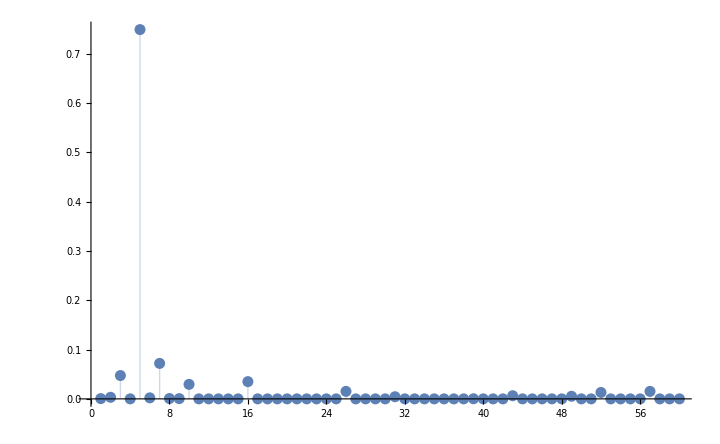

```mathematica
//ListPlot[#, PlotRange->All, Filling->Axis]&(*//imageify*)
```

```mathematica
ImportString[" 5.12554717e-03 -8.32414713e-02 -3.18862431e-01  6.05340736e-01
  4.25586543e-03  1.18066960e-03  3.63237758e-03  2.07636886e-03
 -6.22454764e-04  2.16624385e-03 -4.50825661e-03  4.04952225e-04
  1.22932915e-03  1.26714652e-03  6.80760162e-04  1.24933780e-04
 -4.67600811e-03 -2.42960310e-01 -3.96518315e-01  1.81081278e-03
  1.51323489e-03  1.43467820e-02  4.68873829e-01 -5.29666755e-02
  3.08407192e-02  1.52018834e-03 -2.62931330e-04 -1.09403748e-01
 -3.69439801e-04 -6.71548904e-03 -2.04006535e-01  1.17372671e-05
  5.74446345e-04 -4.04484059e-04  2.15135890e-04  2.73260888e-03
  7.09875694e-04 -2.10296702e-08 -4.09195611e-02  3.84890472e-04
 -3.34491694e-04  3.88819323e-04  2.31597826e-03  8.24025561e-02
 -1.43087084e-04 -5.11956574e-04  2.67422394e-04 -1.45004785e-04
  4.88614737e-02 -1.59880214e-04 -7.68299381e-04 -5.59603641e-04
  4.31074199e-03  8.51691509e-02  1.01836900e-01 -1.56156720e-02
  4.87446991e-02  2.78635978e-03  2.13021444e-03 -5.59300177e-04", "Table"]//Flatten//#^2&//ListPlot[#, PlotRange->All, Filling->Axis]&//imageify
```

```mathematica
neutralWeights.DiagonalMatrix[neutralFreqs^2].neutralWeights//Sqrt[#]*219475.6&
```

```mathematica
neutTF=IdentityMatrix[Length@neutralFreqs];
neutTF[[1]]=neutralWeights;
neutTF=neutTF//Orthogonalize;
neutNewF=neutTF.DiagonalMatrix[neutralFreqs^2].Transpose[neutTF];
```

```mathematica
neutralModes//Dimensions
```

{60,66}

#### Maximally Coupled Modes

```mathematica
neutTFModes=neutTF.neutralModes;
```

```mathematica
{neutSubF,neutSubTF}=Eigensystem[neutNewF[[2;;, 2;;]]];
```

```mathematica
neutTF1=Prepend[
PadLeft[#, Length[neutSubF]+1]&/@neutSubTF,
IdentityMatrix[Length[neutSubF]+1][[1]]
];
```

```mathematica
neutTFModes2=neutTF1.neutTF.neutralModes;
```

```mathematica
neutNewF2=neutTF1.neutNewF.Transpose[neutTF1];
```

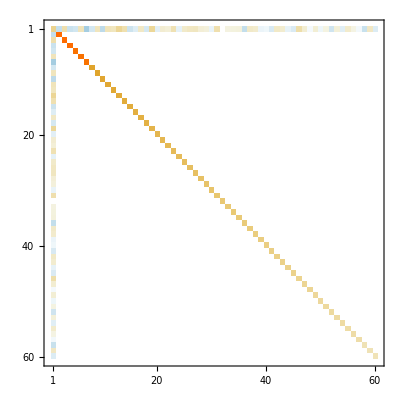

```mathematica
neutTF1.neutNewF.Transpose[neutTF1]//Threshold//MatrixPlot
```

```mathematica
{neutSubF,neutSubTF}=Eigensystem[neutNewF[[2;;, 2;;]]];
```

```mathematica
neutTF1=Prepend[
PadLeft[#, Length[neutSubF]+1]&/@neutSubTF,
IdentityMatrix[Length[neutSubF]+1][[1]]
];
```

```mathematica
neutNewF2=neutTF1.neutNewF.Transpose[neutTF1];
```

```mathematica
newTFVec2=
Prepend[
LeastSquares[
{IdentityMatrix[Length[neutNewF2]][[1]]}//Transpose,
neutNewF2[[;;, 2;;]]
][[1]],
0
];
```

```mathematica
neutTFSub2=Prepend[
PadLeft[#, Length[neutSubF]+1]&/@neutSubTF,
IdentityMatrix[Length[neutSubF]+1][[1]]
];
```

```mathematica
newTFVec.neutNewF2.newTFVec
```

2.86735×10^-13

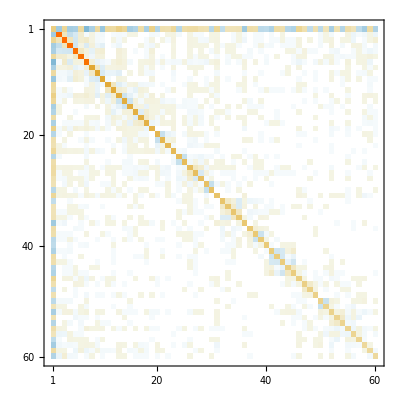

```mathematica
neutNewF2//MatrixPlot
```

##### New GS

We want to choose a vector q and then have construct a space of alternate vectors such that

q^T Fv = 0

and then from this we can find the best unitary approximant

Starting from a basis such that

q^T F v_i = c_i
v_i^T F v_j = ω_ii δ_ij

we can let v_1 be chosen to have the maximum c_i

We then need to find a_1 such that

u_1 = v_1-a_1 q
q^T F u_1 = 0

which implies

u_1 = v_1-a_1 q
a_1 = (q^T F v_1)/(q^T Fq)
= c_1/ω_1

In modified Gram-Schmidt fashion, however, we choose to apply this correction to every basis vector at once, this yields a transformation to a space where everything (else) has been orthogonalized at once

We then need to find the best unitary transformation to this partially orthogonalized basis since the core of the approach is unitary transformations of the normal modes

```mathematica
gsVecs1=Join[
neutTF1[[;;1]],
neutTF1[[2;;]]-(neutNewF2[[1, 2;;]]/neutNewF2[[1, 1]])*ConstantArray[neutTF1[[1]], Length@neutNewF2[[1, 2;;]]]
];
```

```mathematica
SingularValueDecomposition[neutNewF2[[;;, 2;;]]][[3]]//Dimensions
```

{59,59}

```mathematica
tfAlt=Prepend[
Prepend[#, 0]&/@SingularValueDecomposition[neutNewF2[[;;, 2;;]]][[1]],
gsVecs1[[1]]
];
```

```mathematica
subOrthogTF[fMat_, k_]:=
Join[
IdentityMatrix[Length@fMat][[;;k]],
Join[ConstantArray[0, k], #]&/@Orthogonalize[
Prepend[
IdentityMatrix[Length[fMat]-k][[2;;]],
fMat[[k, k+1;;]]
]
]
];
subOrthog[fMat_, k_]:=
With[{tf=subOrthogTF[fMat, k]},
tf.fMat.Transpose[tf]
];
subOrthogAll[fMat_, k_]:=
With[{tf=subOrthogTF[fMat, k]},
{tf,tf.fMat.Transpose[tf]}
];
subOrthogIter[ogFMat_, steps_]:=
Fold[
subOrthog,
ogFMat,
Range[steps]
];
subOrthogAllIter[ogFMat_, steps_]:=
Fold[
With[{dd=subOrthogAll[#[[2]], #2]},
{dd[[1]].#[[1]], dd[[2]]}
]&,
{IdentityMatrix[Length@ogFMat],ogFMat},
Range[steps]
];
subDiagTF[mat_, kmin_, kmax_]:=
Block[{
fullTF=IdentityMatrix[Length@mat],
subtf=Eigenvectors[mat[[kmin;;kmax, kmin;;kmax]]]
},
fullTF[[kmin;;kmax, kmin;;kmax]]=subtf;
fullTF
]
subDiag[mat_, kmin_, kmax_]:=
Block[{
fullTF=subDiagTF[mat, kmin, kmax]
},
fullTF.mat.Transpose[fullTF]
];
obliqueTF[fMat_]:=
Block[{
nodim,ndF, ndG,
newF,newG,
freqs,tf,
svd,
q,p,pi
},
nodim=Power[Diagonal[fMat], 1/4];
ndF=DiagonalMatrix[1/nodim].fMat.DiagonalMatrix[1/nodim];
ndG=DiagonalMatrix[nodim^2];
{freqs,tf}=Eigensystem[{ndF, Inverse@ndG}];
svd=SingularValueDecomposition[DiagonalMatrix[1/Sqrt[freqs]].tf];
q=svd[[1]].Transpose[svd[[3]]];
p=Transpose[q].tf;
pi=Inverse[p];
newF=p.ndF.p;
newG=pi.ndG.pi;
(*newF=pi.ndF.pi;
newG=p.ndG.p;*)
{p, newF, newG, ndF, ndG}
]
```

```mathematica
Export["~/Desktop/bleh.dat", subDiag[neutF4ObMat, 6, 60]]
```

~/Desktop/bleh.dat

```mathematica
Position[
subDiag[neutF4ObMat, 6, 60][[5, 6;;]]//Abs//Sqrt[#]*219475.6&,
_?(#>300&)
]
```

{{9},{15},{19},{27},{36},{53}}

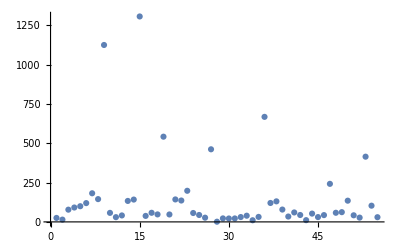

```mathematica
subDiag[neutF4ObMat, 6, 60][[5, 6;;]]//Abs//Sqrt[#]*219475.6&//ListPlot[#, PlotRange->All]&
```

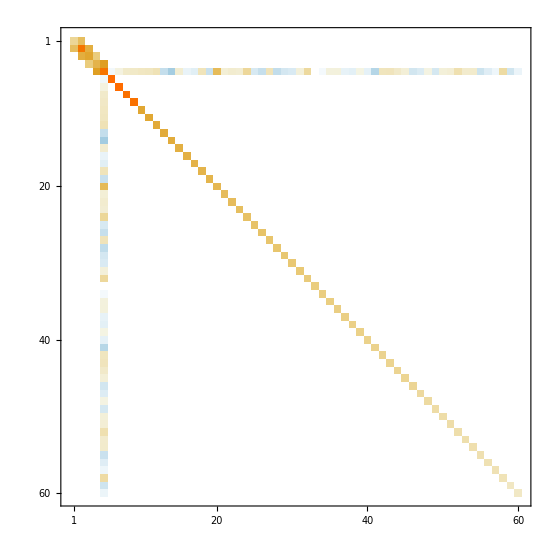

```mathematica
subDiag[neutF4ObMat, 6, 60]//Threshold//MatrixPlot
```

```mathematica
neutF4ObU=Import["~/Desktop/bleh_u.dat"];
neutF4ObFNew=Import["~/Desktop/bleh_f.dat"];
```

```mathematica
neutF4ObFNew[[;;5, ;;5]]*219475.6
```

{{334.645,448.014,-120.483,40.044,-14.0668},{448.014,3424.45,501.208,-33.8185,9.26501},{-120.483,501.208,1625.18,257.779,-48.2032},{40.044,-33.8185,257.779,1202.72,853.82},{-14.0668,9.26501,-48.2032,853.82,3366.64}}

```mathematica
neutF4ObMat[[;;5 ,;;5]]//Eigenvalues//Sqrt[#]*219475.6&
```

{3688.56,3604.62,1625.48,890.335,240.627}

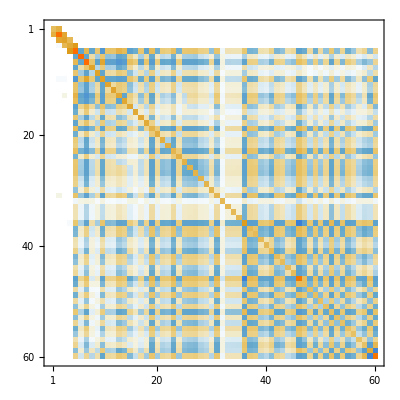

```mathematica
neutF4ObMat//MatrixPlot
```

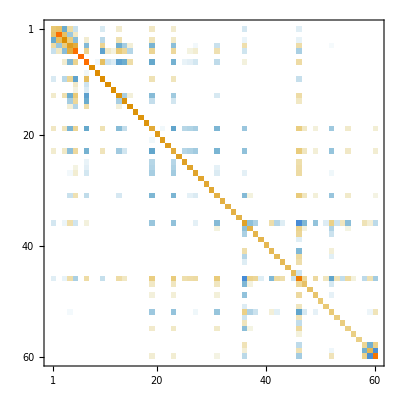

```mathematica
Threshold[neutF4ObFNew, 5/219475.6]//MatrixPlot
```

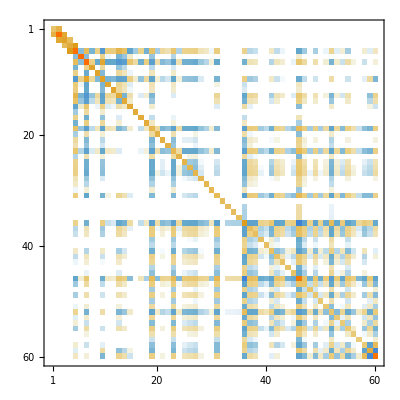

```mathematica
Threshold[neutF4ObMat, (15/219475.6)^2]//MatrixPlot
```

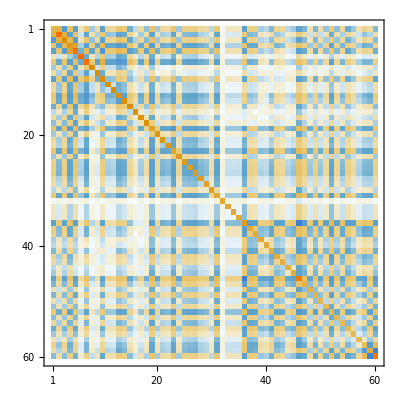

```mathematica
neutF4ObFNew//MatrixPlot
```

{0.985939,1.11371,1.05401,1.13695,1.02402}

{-0.00187856,0.00524516,-0.000864938,-0.0000446416,-1.65988×10^-6}

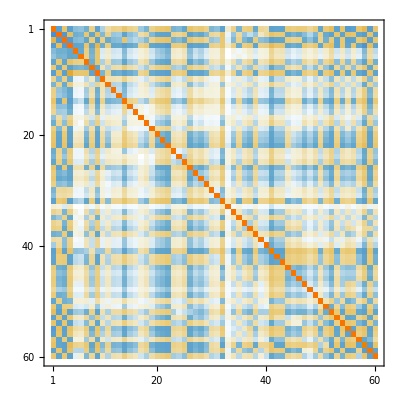

```mathematica
bleh=obliqueTF[subDiag[neutF4ObMat, 5, 60]];
bleh[[1]]//Diagonal//#[[;;5]]&
(bleh[[2]]-bleh[[3]])[[1, ;;5]]
bleh[[1]]//Threshold//MatrixPlot
```

```mathematica
neutTFModes3=subOrthogTF[neutNewF2, 1].neutTFModes2;
neutTFModes4=subOrthogTF[neutNewF3, 2].neutTFModes3;
```

```mathematica
neutF4ObMat=subOrthogIter[neutNewF2, 4];
```

```mathematica
{neutTFModes6TF,neutTFModes6FMat}=subOrthogAllIter[neutNewF2, 4];
neutTFModes6=subDiagTF[neutTFModes6FMat, 6, 60].neutTFModes6TF.neutTFModes2;
```

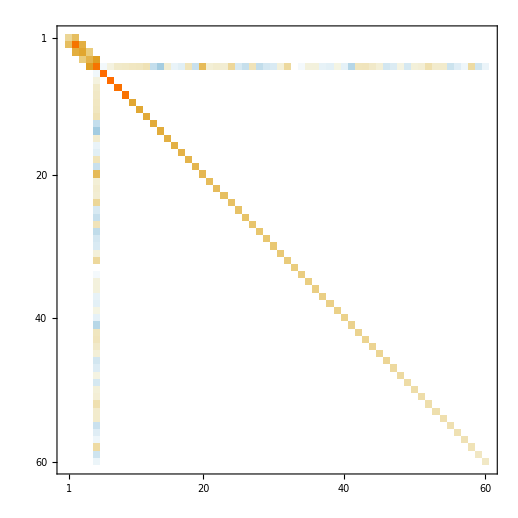

```mathematica
subDiag[neutTFModes6FMat, 6, 60]//Threshold//MatrixPlot
```

```mathematica
animateModes[
atomString,
melemBonds,
neutralCoords
][
Map[Function[#/Sqrt[massVec]//Normalize],neutTFModes6]/50//Transpose,
ViewPoint->{-0.2507654573036361, 1.9541899041773798, 
  0.34388734177707386},
ViewAngle->  0.7232701660000797, ViewVertical->{0.964391188602559, 0.25761115293690473, 
  0.0598842986788867}
]
```

```mathematica
animateModes[
atomString,
melemBonds,
neutralCoords
][
Map[Function[#/Sqrt[massVec]//Normalize],neutralModes]/50//Transpose,
ViewPoint->{-0.2507654573036361, 1.9541899041773798, 
  0.34388734177707386},
ViewAngle->  0.7232701660000797, ViewVertical->{0.964391188602559, 0.25761115293690473, 
  0.0598842986788867}
]
```

```mathematica
subDiag[
subOrthogIter[
subDiag[subOrthogIter[neutNewF2, 1], 3, 60],
2
],
 3, 60
]//Threshold//#[[;;2, ;;2]]&
```

{{6.83961×10^-6,0.0000336746},{0.0000336746,0.000252858}}

```mathematica
neutF4ObMat[[;;2, ;;2]]
```

{{6.83961×10^-6,0.0000336746},{0.0000336746,0.000252858}}

```mathematica
subDiag[neutF4ObMat, 3, 60][[2, 3;;]]//Norm//Sqrt[#]*219475.6&
```

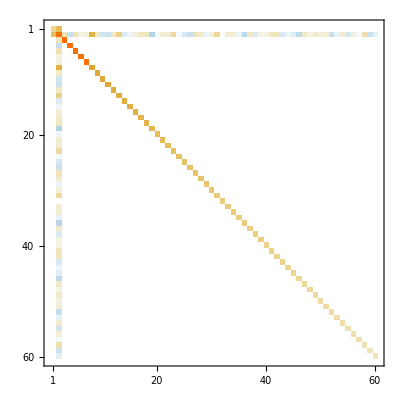

```mathematica
subDiag[neutF4ObMat, 3, 60]//Threshold//MatrixPlot
```

```mathematica
{neutF4Freqs, neutF4TF}=Eigensystem[subOrthogAllIter[neutNewF2, 4]];
neutF4Freqs=subDiag[neutF4ObMat, 5, 60]
```

```mathematica
neut
```

```mathematica
animateModes[
atomString,
melemBonds,
neutralCoords
][
Map[Function[#/Sqrt[massVec]//Normalize],subOrthogAllIter[neutNewF2, 4][[1]].neutTFModes2]/100//Transpose,
ViewPoint->{-0.2507654573036361, 1.9541899041773798, 
  0.34388734177707386},
ViewAngle->  0.7232701660000797, ViewVertical->{0.964391188602559, 0.25761115293690473, 
  0.0598842986788867}
]
```

```mathematica
neutNewF2//Threshold//MatrixPlot
```

-Graphics-

```mathematica
Table[
subOrthogIter[neutNewF2, n][[n+1, n+2;;]]//Norm//219475.6*Sqrt[#]&,
{n, 58}
]
```

{1570.84,812.735,1947.92,1487.03,711.381,1216.31,2320.43,764.831,1769.32,1468.05,555.285,1051.41,2286.29,736.223,2454.65,1194.18,840.508,613.403,718.737,562.749,791.05,892.577,686.578,918.885,885.378,606.491,730.769,868.675,748.317,839.528,816.558,603.656,655.806,771.099,677.879,365.588,840.732,728.315,785.84,434.75,558.796,548.409,460.51,521.851,540.748,592.632,444.975,289.934,386.893,124.026,366.161,279.911,368.824,323.29,246.32,84.2968,480.082,397.958}

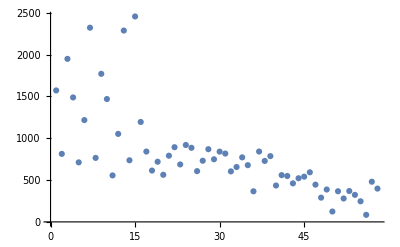

```mathematica
Table[
subOrthogIter[neutNewF, n][[n+1, n+2;;]]//Norm//219475.6*Sqrt[#]&,
{n, 58}
]//ListPlot
```

```mathematica
subOrthogIter[neutNewF, 3][[4, 5;;]]//Norm//219475.6*Sqrt[#]&
```

1947.92

```mathematica
subOrthogIter[neutNewF, 2][[3, 4;;]]//Norm//219475.6*Sqrt[#]&
```

```mathematica
subOrthogIter[fullTF.suborthedF.Transpose[fullTF], 4]
```

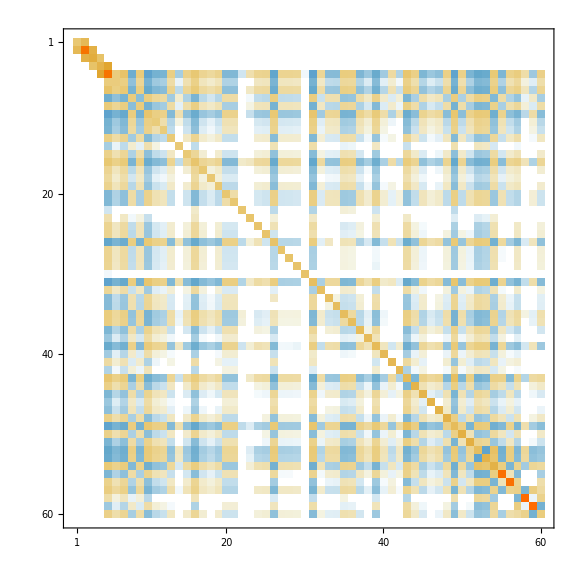

```mathematica
subOrthogIter[fullTF.suborthedF.Transpose[fullTF], 4]//Threshold//MatrixPlot
```

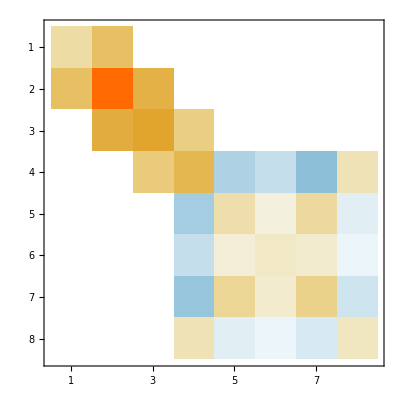

```mathematica
subOrthogIter[neutNewF, 3][[;;8, ;;8]]//Threshold//MatrixPlot
```

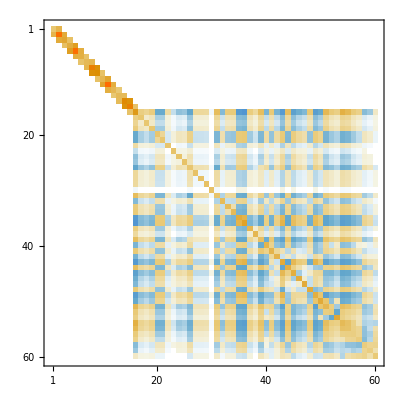

```mathematica
subOrthogIter[neutNewF, 15]//Threshold//MatrixPlot
```

```mathematica
tfOrtho=
Prepend[
Prepend[#, 0]&/@Orthogonalize[
Prepend[
IdentityMatrix[Length[neutNewF2]-1][[2;;]],
neutNewF2[[1, 2;;]]
]
],
IdentityMatrix[Length@neutNewF2][[1]]
];
```

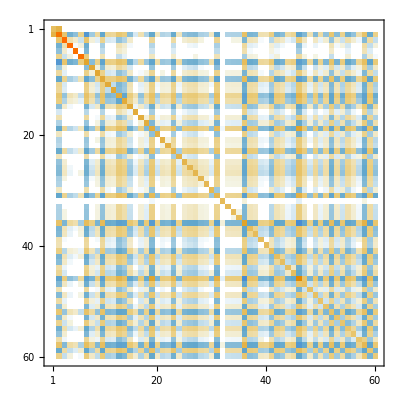

```mathematica
tfOrtho2=subOrthog[neutNewF2, 1];
neutNewF3=tfOrtho2.neutNewF2.Transpose[tfOrtho2];
neutNewF3//Threshold//MatrixPlot
```

```mathematica
neutNewF4[[1, 2;;]]//Norm
```

0.0000336746

```mathematica
neutNewF4[[2, 3;;]]//Norm
```

0.000051226

```mathematica
neutNewF4[[3, 4;;]]//Norm
```

0.0000137128

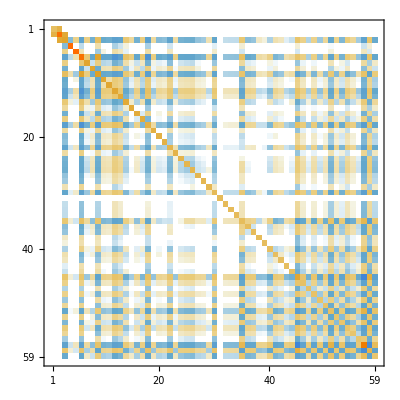

```mathematica
tfOrtho3=subOrthog[neutNewF3, 2];
neutNewF4=tfOrtho3.neutNewF3.Transpose[tfOrtho3];
neutNewF4//Threshold//MatrixPlot
```

```mathematica
neutNewF2[[1, 2;;]]
```

```mathematica
SingularValueDecomposition[neutNewF2[[;;, 2;;]]][[1]]
```

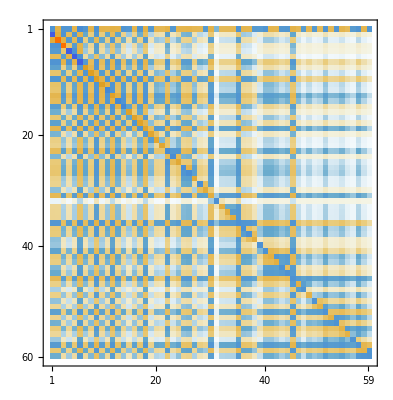

```mathematica
tfAlt.neutNewF2[[;;, 2;;]]//MatrixPlot
```

```mathematica
unitTF1=Prepend[
Map[
PadLeft[#, Length[neutSubF]+1]&,
Transpose[#[[1]]].#[[3]]&@SingularValueDecomposition[gsVecs1[[2;;,2;;]]]
],
gsVecs1[[1]]
];
```

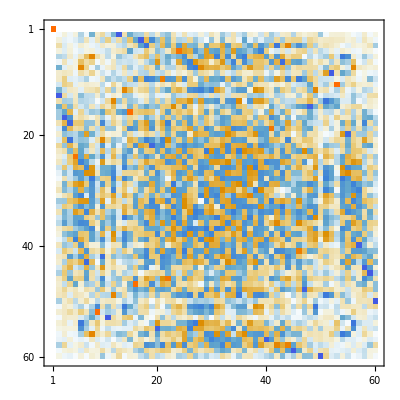

```mathematica
unitTF1//MatrixPlot
```

## Franck-Condon Factors

In the Franck-Condon approximation we obtain our intensities by evaluating the integral between g_n, the nth vibrational state (as a product) on the ground electronic surface and e_m the mth vibrational state on the electronic excited state

By writing

g_n(x) = N_n P_n^(g)(x-ξ^(g))𝒩(Σ^(g), ξ^(g))

where 𝒩(Σ^(g), ξ^(g)) is a normal distribution with covariance matrix Σ^(g) centered at ξ^(g), P_n^(g)(x-ξ^(g)) is the nth product Hermite polynomial expressed in the basis that diagonalizes Σ^(g), and N_n is the corresponding normalization factor

So we get

∫_(ℝ^D) g_n(x)e_m(x) = N_n N_m∫_(ℝ^D) P_n^(g)(x-ξ^(g))𝒩(Σ^(g), ξ^(g))P_m^(e)(x-ξ^(e))𝒩(Σ^(e), ξ^(e))

and as previously established for a DGB, we can write this in terms of a single Gaussian term by writing

𝒩(Σ^(g), ξ^(g))𝒩(Σ^(e), ξ^(e)) = 𝒩(Σ^(g)+Σ^(g), ξ^(g)-ξ^(e))𝒩(Σ^(c), ξ^(c))

where 𝒩(Σ^(c), ξ^(c)) is the Gaussian in the weighted center of 𝒩(Σ^(g), ξ^(g)) and 𝒩(Σ^(e), ξ^(e))

Σ^((c)-1) = Σ^((g)-1)+Σ^((e)-1)
ξ^(c) = Σ^(c)(Σ^((g)-1)ξ^(g)+Σ^((e)-1)ξ^(e))

and in principle we could express the total integral in terms of a single Gaussian and single polynomial, however the number of terms required to store and compute the polynomial grows exponentially and the process cannot be easily parallelized

##### Coordinate Simplifications

Therefore we will introduce two alternate coordinate sets,

x^(g) = Q^(g)x
x^(e) = Q^(e)x

where Q^(g) is the transformation that diagonalizes Σ^(g) and the same for Q^(e)

These are the coordinates in which g_n is a product of Hermite 1D polynomials and Gaussians (and similarly for e_m)

This means the key integral is

∫_(ℝ^D) H_n^(g)(x^(g)-Q^(g)ξ^(g))H_m^(e)(x^(e)-Q^(e)ξ^(e))𝒩(Σ^(c), ξ^(c))

and now we can transform to shifted coordinates by writing

x^(g)-Q^(g)ξ^(g) = x^(g)-Q^(g)ξ^(c) + Q^(g)(ξ^(c)-ξ^(g))
=

giving us new, still pretty sparse, polynomials of the form

H_n^(g)(x^(g)-Q^(g)ξ^(g)) = J_n^(g)(x^(g)-Q^(g)ξ^(c))

#### Term-by-Term Evaluation

Finally, we get to the heart of the problem, we have the integral

∫_(ℝ^D) J_n^(g)(x^(g)-Q^(g)ξ^(c))J_m^(e)(x^(e)-Q^(e)ξ^(c))𝒩(Σ^(c), ξ^(c))

and generically, we handle this by transforming to the coordinate system that diagonalizes Σ^(c), in which we have a simple product of 1D Gaussians, i.e. we get

∫_(ℝ^D) J_n^(g)(Q^(c)ᵀ(x^(g)-Q^(g)ξ^(c)))J_m^(e)(Q^(c)ᵀ(x^(e)-Q^(e)ξ^(c)))𝒩(1/2 α^(c), Q^(c)ᵀ ξ^(c))

but this provides an inconvenient evaluation strategy, instead we’ll write

y^(g) = x^(g)-Q^(g)ξ^(c)

and write

J_n^(g)(y^(g))J_m^(e)(y^(e)) = ∑_(s,t) (J_n^(g))_s(J_m^(e))_t∏_i (y_i^(g))^s_i(y_i^(e))^t_i

where the summation is over every term index in J_n^(g) and J_m^(e)

The question then becomes, under what conditions do we have

∫_(x∈ℝ^D) ∏_i (y_i^(g))^s_i(y_i^(e))^t_i 𝒩(1/(2 α^(c)), Q^(c)ᵀ ξ^(c)) ≠ 0

and by symmetry properties of Gaussians we have n = ∑_i s_i+t_i must be even

THIS NEEDS SOME CLEAN UP WORK FOR PRECISION

Now we can recall that

y^(g) = Q^(c)ᵀQ^(g)(x-ξ^(c))

and so letting

L^(g) = Q^(c)ᵀ Q^(g)

we get

(y_i^(g))^s_i = (⊗_s_i L_i^(g))⊙(x-ξ^(c))^s_i
= ∑_(r∈Ξ(s_i)) M_r ∏_j ((L_ij^(g))^r_j)(x-ξ^(c))_j^r_j

where Ξ(s_i) is the set of upper-triangular indices for an s_i-dimensional array over the coordinates and M_r is the associated multinomial coefficient

Finally letting z = Q^(c)ᵀ(x-ξ^(c)) we get

∫_(z∈ℝ^d) 𝒩(1/(2 α^(c)))∏_j ((L_ij^(g))^r_j)z_j^r_j = ∏_j ((L_ij^(g))^r_j) ∫_(z∈ℝ) z_j^r_j 𝒩(1/(2 α_j^(c)))
= ∏_j ((L_ij^(g))^r_j)𝒢(r_j, α_j^(c))

where [CHECK THIS]

𝒢(k, α) = ∫_(z∈ℝ) z^k 𝒩(1/(2α))
= Piecewise[{{(α^(-(2k+1))/π)^(1/4)Γ((k+1)/2), p_k even}, {0, else}}]

Giving us in total (accounting for both the ground and excited state coordinates),

∫_(ℝ^D) ...𝒩(Σ^(c), ξ^(c)) =
∑_(s,t) (J_n^(g))_s(J_m^(e))_t∑_(r^(g)∈Ξ(s_i)
r^(e)∈Ξ(t_i)) M_(r^(g))∏_j ((L_ij^(g))^(r_j^(g)))((L_ij^(e))^(r_j^(e)))𝒢(r_j^(g)+r_j^(e),α_j^(c))

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/fc_integrals.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/fc_integrals.pdf

n q^s n+k = P_((s-k)/2)^((s+k)/2)(n)√(n+1)√(n+2)... √(n+k)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/generic_matrix_element.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/generic_matrix_element.pdf

n^(0)An+k^(0) = ∑_(p∈diagrams(A,k)) (coeffs(A,p))/(energies(p))P_p^[A](n)

```mathematica
Export[
"/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/generic_poly.pdf", 
NotebookRead[PreviousCell[]]
]
```

/Users/Mark/Documents/Postdoc/Presentations/GM_8_23_2024/generic_poly.pdf

##### Counting Problems

While this does provide a general formula for the evaluation of these integrals, the computational complexity is significantly worse than simply multiplying the two shifted polynomials using a FFT-based convolution

On the other hand, this approach allows us to fully exploit the symmetries in 𝒢 by noting that, given some s and t, we need only to consider the totally even r_j^(g)+r_j^(e)

In practice, we can reduce these evaluations over the different possible classes of terms. By reindexing, WLOG we can for instance consider all of the terms that arise from a transition from the ground state to a state with 4 quanta of excitation, which will generate terms involving 0, 2, and 4 coordinates respectively. Considering just the 4-coordinate terms we have 5 classes of terms, x_1^4, x_1^3 x_2, x_1^2 x_2^2, x_1^2 x_2 x_3, x_1 x_2 x_3 x_4, corresponding to the different integer partitions

Each of these terms in turn will generate a set of non-zero integrals, corresponding to either putting all 4 quanta into one coordinate or 2 in one and 2 in another, i.e. the two totally even integer partitions

Finally, we need to consider the different possible permutations. The all-in-one case is simple as there are no permutations, but the two-and-two case has 6 attendant perms which we can enumerate as

(i i j j)
(i j i j)
(j i i j)
(j i j i)
(j j i i)
(i j j i)

We then need to split these over the corresponding coordinates, e.g. for the x_1^3 x_2 and x_1^2 x_2^2 cases we get (letting the commas indicate the splits)

x_1^3 x_2
(i i j, j)
(i j i, j)
(j i i, j)
(j i j, i)
(j j i, i)
(i j j, i) | x_1^2 x_2^2
(i i, j j)
(i j, i j)
(j i, i j)
(j i, j i)
(j j, i i)
(i j, j i)

which we can now reduce by symmetry, to give a table like

x_1^4 =>  6(i i j j)
x_1^3 x_2 => 3(i i j, j) + 3(i j j, i) 
x_1^2 x_2 x_3 => (i i, j, j) + 2(i j, i, j) + 2(i j, j, i) + (j j, i, i)

this is, at some level, a 2D integer partition problem, where we need to e.g. split (2,2) over (3,1) or (2,1,1)

There is a straightforward, efficient enough approach to handling this class of problem. We treat this recursively, noting that, e.g. given the box (2,1,1), we can start from the right and consider that the 1 indicates we can either take element i or element j and put it in this box, i.e. we consider the two permutations of (1,0), taking the first of these, we now have the boxes (2,1) to split (1,2) over. Generically this means given a current state (b_1,...,b_k) and terms (n_1^(k),...,n_N^(k)) we consider the padded integer partition permutations of b_k that will keep (n_1^(k−1),...,n_N^(k−1)) entirely nonnegative. Once we are down to b_1, we simply get to use the current value of (n_1^(1),...,n_N^(1)) as the final term